## Just τ dependence

### Generalities

#### Metric and Connection

```mathematica
Needs["Greater2`"];
```

GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents

Needs::nocont: Context Greater2` was not created when Needs was evaluated.

```mathematica
Clear[p,u]
gp = {{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2 r^2,0,0},{0,0,0,p^2/l^2 r^2 Cos[θ]^2,0},{0,0,0,0,1/g[p]}}
X= {t,r,θ,ϕ,p};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gp//MatrixForm 
Simplify[Det[gp]]
Γp=Christoffel[gp, X]/.p->p[τ]
gpτ=gp/.p->p[τ]
(*/.{g[p]->g[p[τ]],g'[p]->g'[p[τ]]}*)
```

{{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,(p^2 r^2)/l^2,0,0},{0,0,0,(p^2 r^2 Cos[θ]^2)/l^2,0},{0,0,0,0,1/g[p]}}

(-g[p] | 0 | 0 | 0 | 0
0 | p^2/l^2 | 0 | 0 | 0
0 | 0 | (p^2 r^2)/l^2 | 0 | 0
0 | 0 | 0 | (p^2 r^2 Cos[θ]^2)/l^2 | 0
0 | 0 | 0 | 0 | 1/g[p])

-(p^6 r^4 Cos[θ]^2)/l^6

{{{0,0,0,0,g'[p[τ]]/(2 g[p[τ]])},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{g'[p[τ]]/(2 g[p[τ]]),0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,1/p[τ]},{0,0,-r,0,0},{0,0,0,-r Cos[θ]^2,0},{0,1/p[τ],0,0,0}},{{0,0,0,0,0},{0,0,1/r,0,0},{0,1/r,0,0,1/p[τ]},{0,0,0,Cos[θ] Sin[θ],0},{0,0,1/p[τ],0,0}},{{0,0,0,0,0},{0,0,0,1/r,0},{0,0,0,-Tan[θ],0},{0,1/r,-Tan[θ],0,1/p[τ]},{0,0,0,1/p[τ],0}},{{1/2 g[p[τ]] g'[p[τ]],0,0,0,0},{0,-(g[p[τ]] p[τ])/l^2,0,0,0},{0,0,-(r^2 g[p[τ]] p[τ])/l^2,0,0},{0,0,0,-(r^2 Cos[θ]^2 g[p[τ]] p[τ])/l^2,0},{0,0,0,0,-g'[p[τ]]/(2 g[p[τ]])}}}

{{-g[p[τ]],0,0,0,0},{0,p[τ]^2/l^2,0,0,0},{0,0,(r^2 p[τ]^2)/l^2,0,0},{0,0,0,(r^2 Cos[θ]^2 p[τ]^2)/l^2,0},{0,0,0,0,1/g[p[τ]]}}

```mathematica
Γp[[;;,;;,2]]
```

{{0,0,0,0,0},{0,0,0,0,1/p[τ]},{0,0,1/r,0,0},{0,0,0,1/r,0},{0,-(g[p[τ]] p[τ])/l^2,0,0,0}}

#### solve for e_(r)

```mathematica
u = {κp/g[p[τ]],r'[τ],0,0,p'[τ]}
nM = {p'[τ]/(g[p[τ]] κr),0,0,0,κp/κr}
```

{κp/g[p[τ]],r'[τ],0,0,p'[τ]}

{p'[τ]/(κr g[p[τ]]),0,0,0,κp/κr}

```mathematica
ert = {erT,erR,0,0,erP} (*temp variables for er*)
erPsol =Solve[ert.gpτ.nM==0,erP][[1]]
erTsol=Solve[(ert.gpτ.u/.erPsol)==0,erT][[1]]
erRsol=Simplify[Solve[(ert.gpτ.ert /.erPsol/.erTsol)==p[τ]^2/l^2,erR][[2]]]
```

{erT,erR,0,0,erP}

{erP→(erT g[p[τ]] p'[τ])/κp}

{erT→(erR κp p[τ]^2 r'[τ])/(l^2 (κp^2-p'[τ]^2))}

{erR→1/(√((l^2 κp^2-l^2 p'[τ]^2-g[p[τ]] p[τ]^2 r'[τ]^2)/(l^2 (κp^2-p'[τ]^2))))}

```mathematica
erRsimped=PowerExpand[Simplify[erRsol/.κp^2->κr^2 g[p[τ]]+p'[τ]^2/.κr^2->1+p[τ]^2/l^2 r'[τ]^2]]
erTsimped=erTsol/.erRsimped/.κp^2->κr^2 g[p[τ]]+p'[τ]^2
erPsimped = Simplify[erPsol/.erTsimped/.κp^2->κr^2 g[p[τ]]+p'[τ]^2/.κr^2->1+p[τ]^2/l^2 r'[τ]^2]
```

{erR→κr}

{erT→(κp p[τ]^2 r'[τ])/(l^2 κr g[p[τ]])}

{erP→(p[τ]^2 p'[τ] r'[τ])/(l^2 κr)}

```mathematica
er=ert/.erRsimped/.erTsimped/.erPsimped
```

{(κp p[τ]^2 r'[τ])/(l^2 κr g[p[τ]]),κr,0,0,(p[τ]^2 p'[τ] r'[τ])/(l^2 κr)}

```mathematica
Simplify[Simplify[er.gpτ.er/.κp^2->κr^2 g[p[τ]]+p'[τ]^2]/.κr^2->1+p[τ]^2/l^2 r'[τ]^2]
Simplify[Simplify[er.gpτ.nM/.κp^2->κr^2 g[p[τ]]+p'[τ]^2]/.κr^2->1+p[τ]^2/l^2 r'[τ]^2]
Simplify[Simplify[er.gpτ.u/.κp^2->κr^2 g[p[τ]]+p'[τ]^2]/.κr^2->1+p[τ]^2/l^2 r'[τ]^2]
```

p[τ]^2/l^2

0

0

### K_ττ

#### Get expression for K_ττ using norm of u

```mathematica
ap = Simplify[p''[τ]+u.(Γp[[5,;;,;;]]).u ]/.κp[τ]->√(κr^2 g[p[τ]]+p'[τ]^2)
(*Simplify[ap/.κr[τ]->√(1+p[τ]^2/l^2 r'[τ]^2)]*)
ar=r''[τ] + u.(Γp[[2,;;,;;]]).u
```

(g'[p[τ]] (κp^2-p'[τ]^2))/(2 g[p[τ]])-(g[p[τ]] p[τ] r'[τ]^2)/l^2+p''[τ]

(2 p'[τ] r'[τ])/p[τ]+r''[τ]

```mathematica
κrdτ = Simplify[D[√(1+p[τ]^2/l^2 r'[τ]^2),τ]]
(*κrdτ =(p[τ]^2 r'[τ] r''[τ])/(l^2 κr)*)
κrdτ = Simplify[(p[τ] r'[τ] (p'[τ] r'[τ]+p[τ] r''[τ]))/(l^2 κr)]
```

(p[τ] r'[τ] (p'[τ] r'[τ]+p[τ] r''[τ]))/(l^2 √(1+(p[τ]^2 r'[τ]^2)/l^2))

(p[τ] r'[τ] (p'[τ] r'[τ]+p[τ] r''[τ]))/(l^2 κr)

```mathematica
κpdτ= D[√(κr[τ]^2 g[p[τ]] + p'[τ]^2),τ]
(*κpdτ=Simplify[(2 g[p] κr OverDot[κr]+2 p'[τ] p''[τ])/(2 κp)]*)
κpdτ=Simplify[1/(2 κp)(κr^2 g'[p[τ]] p'[τ]+2 g[p[τ]] κr OverDot[κr]+2 p'[τ] p''[τ])]
```

(κr[τ]^2 g'[p[τ]] p'[τ]+2 g[p[τ]] κr[τ] κr'[τ]+2 p'[τ] p''[τ])/(2 √(g[p[τ]] κr[τ]^2+p'[τ]^2))

(2 κr g[p[τ]] OverDot[κr]+p'[τ] (κr^2 g'[p[τ]]+2 p''[τ]))/(2 κp)

```mathematica
arofκ=Simplify[ar/.Solve[κrdτ==OverDot[κr],r''[τ]][[1]]]
arofκ = (l^2 κr OverDot[κr])/(p[τ]^2 r'[τ])+(p'[τ] r'[τ])/p[τ]
```

(l^2 κr OverDot[κr]+p[τ] p'[τ] r'[τ]^2)/(p[τ]^2 r'[τ])

(l^2 κr OverDot[κr])/(p[τ]^2 r'[τ])+(p'[τ] r'[τ])/p[τ]

```mathematica
apofκ=FullSimplify[ap/.Solve[κpdτ==OverDot[κp],p''[τ]][[1]]]
(*apofκ =Simplify[(κp OverDot[κp]-κr g[p[τ]] OverDot[κr])/p'[τ]-(p[τ] g[p[τ]] r'[τ]^2)/l^2]*)
```

(κp OverDot[κp]-κr g[p[τ]] OverDot[κr])/p'[τ]-(g'[p[τ]] (-κp^2+κr^2 g[p[τ]]+p'[τ]^2))/(2 g[p[τ]])-(g[p[τ]] p[τ] r'[τ]^2)/l^2

```mathematica
(*/.κr[τ]->√(1/g[p[τ]](κp[τ]^2-p'[τ]^2))]*)
Kττ=FullSimplify[- ap κr/κp+ar/(κp κr)p^2/l^2 r'[τ]p'[τ]]
```

(κr^2 ((g'[p[τ]] (-κp^2+p'[τ]^2))/(2 g[p[τ]])+(g[p[τ]] p[τ] r'[τ]^2)/l^2-p''[τ])+(p^2 p'[τ] r'[τ] ((2 p'[τ] r'[τ])/p[τ]+r''[τ]))/l^2)/(κp κr)

```mathematica
Kττofκs = Simplify[FullSimplify[- apofκ κr/κp+arofκ/(κp κr)p[τ]^2/l^2 r'[τ]p'[τ]]/.κr^2 g[p[τ]]+p'[τ]^2->κp^2]
(*Simplify[(-κr^2 OverDot[κp]+(κp (l^2 κr OverDot[κr]+p[τ] p'[τ] r'[τ]^2))/l^2)/(κr p'[τ])]*)
```

-(κr OverDot[κp])/p'[τ]+(κp OverDot[κr])/p'[τ]+(κp p[τ] r'[τ]^2)/(l^2 κr)

#### Solve the Junction condition for Ṙ

```mathematica
Solve[-(1+p^2/l^2 rp)Pσ'[p]+Pσ[p] √(1+p^2/l^2 rp)D[√(1+p^2/l^2 rp),p] ==Pσ[p]/p,rp]
Expand[FullSimplify[%/.{Pσ[p]->p σ[p],Pσ'[p]->D[p σ[p],p]}]]
FullSimplify[1+p^2/l^2 rp/.%]
```

{{rp→-(l^2 (Pσ[p]+p Pσ'[p]))/(p^2 (-Pσ[p]+p Pσ'[p]))}}

{{rp→-l^2/p^2-(2 l^2 σ[p])/(p^3 σ'[p])}}

{-(2 σ[p])/(p σ'[p])}

```mathematica
Get expression for Subscript[K, ττ] using norm of u
```

{(expression for Get norm of using κp K_ττ)/g[p[τ]],expression for Get norm of using K_ττ r'[τ],0,0,expression for Get norm of using K_ττ p'[τ]}

```mathematica
Get expression for Subscript[K, ττ] using norm of u
```

{(expression for Get norm of using κp K_ττ)/g[p[τ]],expression for Get norm of using K_ττ r'[τ],0,0,expression for Get norm of using K_ττ p'[τ]}

```mathematica
Get expression for Subscript[K, ττ] using norm of uGet expression for Subscript[K, ττ] using norm of u
```

{(expression^2 for^2 Get norm^2 of^2 uGet using^2 κp K_ττ^2)/g[p[τ]],expression^2 for^2 Get norm^2 of^2 uGet using^2 K_ττ^2 r'[τ],0,0,expression^2 for^2 Get norm^2 of^2 uGet using^2 K_ττ^2 p'[τ]}

#### Get expression for K_ττ directly

```mathematica
uτ={κp[τ]/g[p[τ]],r'[τ],0,0,p'[τ]}
nMτ= {p'[τ]/(κr[τ] g[p[τ]]),0,0,0,κp[τ]/κr[τ]}
```

{κp[τ]/g[p[τ]],r'[τ],0,0,p'[τ]}

{p'[τ]/(g[p[τ]] κr[τ]),0,0,0,κp[τ]/κr[τ]}

```mathematica
κrdτ = Simplify[D[√(1+p[τ]^2/l^2 r'[τ]^2),τ]]
κpdτ=Simplify[ D[√(κr[τ]^2 g[p[τ]] + p'[τ]^2),τ]]
```

(p[τ] r'[τ] (p'[τ] r'[τ]+p[τ] r''[τ]))/(l^2 √(1+(p[τ]^2 r'[τ]^2)/l^2))

(κr[τ]^2 g'[p[τ]] p'[τ]+2 g[p[τ]] κr[τ] κr'[τ]+2 p'[τ] p''[τ])/(2 √(g[p[τ]] κr[τ]^2+p'[τ]^2))

```mathematica
Rpp=PowerExpand[Simplify[Solve[κrdτ==κr'[τ],r''[τ]][[1]]]]
Ppp=PowerExpand[Simplify[Solve[κpdτ==κp'[τ],p''[τ]][[1]]/.Rpp]/.p'[τ]^2->κp[τ]^2-g[p[τ]] κr[τ]^2]
```

{r''[τ]→(-p[τ] p'[τ] r'[τ]^2+l^2 √(1+(p[τ]^2 r'[τ]^2)/l^2) κr'[τ])/(p[τ]^2 r'[τ])}

{p''[τ]→-(κr[τ]^2 g'[p[τ]] p'[τ]-2 κp[τ] κp'[τ]+2 g[p[τ]] κr[τ] κr'[τ])/(2 p'[τ])}

```mathematica
Expand[Simplify[uτ.D[gpτ.nMτ,τ]]];
Expand[%/.Ppp]
%-Expand[Sum[(uτ.(Γp[[i,;;,;;]]).uτ)(nMτ.gpτ)[[i]],{i,5}]]
Simplify[%/.κp[τ]^2->(g[p[τ]] κr[τ]^2+ p'[τ]^2)]
Simplify[%/.κp[τ]^2->(g[p[τ]] κr[τ]^2+ p'[τ]^2)]
```

(κp[τ] κr[τ] g'[p[τ]])/(2 g[p[τ]])-(κp[τ] g'[p[τ]] p'[τ]^2)/(g[p[τ]]^2 κr[τ])-(κp[τ]^2 κp'[τ])/(g[p[τ]] κr[τ] p'[τ])+(p'[τ] κp'[τ])/(g[p[τ]] κr[τ])+(κp[τ] κr'[τ])/p'[τ]

-(κp[τ]^3 g'[p[τ]])/(2 g[p[τ]]^2 κr[τ])+(κp[τ] κr[τ] g'[p[τ]])/(2 g[p[τ]])+(κp[τ] g'[p[τ]] p'[τ]^2)/(2 g[p[τ]]^2 κr[τ])+(p[τ] κp[τ] r'[τ]^2)/(l^2 κr[τ])-(κp[τ]^2 κp'[τ])/(g[p[τ]] κr[τ] p'[τ])+(p'[τ] κp'[τ])/(g[p[τ]] κr[τ])+(κp[τ] κr'[τ])/p'[τ]

1/2 ((κp[τ] κr[τ] g'[p[τ]])/g[p[τ]]+(κp[τ] g'[p[τ]] (-κp[τ]^2+p'[τ]^2))/(g[p[τ]]^2 κr[τ])+(2 p[τ] κp[τ] r'[τ]^2)/(l^2 κr[τ])+(2 (-κr[τ] κp'[τ]+κp[τ] κr'[τ]))/p'[τ])

(p[τ] κp[τ] r'[τ]^2)/(l^2 κr[τ])+(-κr[τ] κp'[τ]+κp[τ] κr'[τ])/p'[τ]

success! :)

## With r dependence (only on p)

### Generalities

#### Metric and Connection

```mathematica
Needs["Greater2`"];
```

GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents

Needs::nocont: Context Greater2` was not created when Needs was evaluated.

```mathematica
gp = {{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2 r^2,0,0},{0,0,0,p^2/l^2 r^2 Cos[θ]^2,0},{0,0,0,0,1/g[p]}}
X= {t,r,θ,ϕ,p};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gp//MatrixForm 
Simplify[Det[gp]]
Γp=Christoffel[gp, X]/.p->p[r,τ]
gprτ=gp/.p->p[r,τ]

(*/.{g[p]->g[p[τ]],g'[p]->g'[p[τ]]}*)
```

{{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,(p^2 r^2)/l^2,0,0},{0,0,0,(p^2 r^2 Cos[θ]^2)/l^2,0},{0,0,0,0,1/g[p]}}

(-g[p] | 0 | 0 | 0 | 0
0 | p^2/l^2 | 0 | 0 | 0
0 | 0 | (p^2 r^2)/l^2 | 0 | 0
0 | 0 | 0 | (p^2 r^2 Cos[θ]^2)/l^2 | 0
0 | 0 | 0 | 0 | 1/g[p])

-(p^6 r^4 Cos[θ]^2)/l^6

{{{0,0,0,0,g'[p[r,τ]]/(2 g[p[r,τ]])},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{g'[p[r,τ]]/(2 g[p[r,τ]]),0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,1/p[r,τ]},{0,0,-r,0,0},{0,0,0,-r Cos[θ]^2,0},{0,1/p[r,τ],0,0,0}},{{0,0,0,0,0},{0,0,1/r,0,0},{0,1/r,0,0,1/p[r,τ]},{0,0,0,Cos[θ] Sin[θ],0},{0,0,1/p[r,τ],0,0}},{{0,0,0,0,0},{0,0,0,1/r,0},{0,0,0,-Tan[θ],0},{0,1/r,-Tan[θ],0,1/p[r,τ]},{0,0,0,1/p[r,τ],0}},{{1/2 g[p[r,τ]] g'[p[r,τ]],0,0,0,0},{0,-(g[p[r,τ]] p[r,τ])/l^2,0,0,0},{0,0,-(r^2 g[p[r,τ]] p[r,τ])/l^2,0,0},{0,0,0,-(r^2 Cos[θ]^2 g[p[r,τ]] p[r,τ])/l^2,0},{0,0,0,0,-g'[p[r,τ]]/(2 g[p[r,τ]])}}}

{{-g[p[r,τ]],0,0,0,0},{0,p[r,τ]^2/l^2,0,0,0},{0,0,(r^2 p[r,τ]^2)/l^2,0,0},{0,0,0,(r^2 Cos[θ]^2 p[r,τ]^2)/l^2,0},{0,0,0,0,1/g[p[r,τ]]}}

#### solve for e_(r)

```mathematica
u = {κp[r,τ]/g[p[r,τ]],D[R[τ],τ],0,0,D[p[r,τ],τ]}
nM = {D[p[r,τ],τ]/(g[p[r,τ]] κr[r,τ]),0,0,0,κp[r,τ]/κr[r,τ]}
```

{κp[r,τ]/g[p[r,τ]],R'[τ],0,0,p^(0,1)[r,τ]}

{(p^(0,1)[r,τ])/(g[p[r,τ]] κr[r,τ]),0,0,0,κp[r,τ]/κr[r,τ]}

```mathematica
ert = {erT,erR,0,0,erP} (*temp variables for er*)
erPsol =Solve[ert.gprτ.nM==0,erP][[1]]
erTsol=Solve[(ert.gprτ.u/.erPsol)==0,erT][[1]]
erRsol=Simplify[Solve[(ert.gprτ.ert /.erPsol/.erTsol)==p[r,τ]^2/l^2,erR][[2]]]
```

{erT,erR,0,0,erP}

{erP→(erT g[p[r,τ]] p^(0,1)[r,τ])/κp[r,τ]}

{erT→(erR p[r,τ]^2 κp[r,τ] R'[τ])/(l^2 (κp[r,τ]^2-(p^(0,1)[r,τ])^2))}

{erR→1/(√((l^2 κp[r,τ]^2-g[p[r,τ]] p[r,τ]^2 R'[τ]^2-l^2 (p^(0,1)[r,τ])^2)/(l^2 (κp[r,τ]^2-(p^(0,1)[r,τ])^2))))}

```mathematica
κprepl=κp[r,τ]^2->κr[r,τ]^2 g[p[r,τ]]+D[p[r,τ],τ]^2;
κrrepl= κr[r,τ]^2->1+p[r,τ]^2/l^2 D[R[τ],τ]^2;
```

```mathematica
erRsimped=PowerExpand[Simplify[erRsol/.κprepl/.κrrepl]]
erTsimped=erTsol/.erRsimped/.κprepl
erPsimped = Simplify[erPsol/.erTsimped/.κprepl/.κrrepl]
```

{erR→κr[r,τ]}

{erT→(p[r,τ]^2 κp[r,τ] R'[τ])/(l^2 g[p[r,τ]] κr[r,τ])}

{erP→(p[r,τ]^2 R'[τ] p^(0,1)[r,τ])/(l^2 κr[r,τ])}

```mathematica
erRsimped=PowerExpand[Simplify[erRsol/.κprepl/.κrrepl]]
erTsimped=erTsol/.erRsimped/.κprepl
erPsimped = Simplify[erPsol/.erTsimped/.κprepl/.κrrepl]
```

{erR→κr[r,τ]}

{erT→(p[r,τ]^2 κp[r,τ] R'[τ])/(l^2 g[p[r,τ]] κr[r,τ])}

{erP→(p[r,τ]^2 R'[τ] p^(0,1)[r,τ])/(l^2 κr[r,τ])}

```mathematica
er=ert/.erRsimped/.erTsimped/.erPsimped
```

{(p[r,τ]^2 κp[r,τ] R'[τ])/(l^2 g[p[r,τ]] κr[r,τ]),κr[r,τ],0,0,(p[r,τ]^2 R'[τ] p^(0,1)[r,τ])/(l^2 κr[r,τ])}

```mathematica
Simplify[Simplify[er.gprτ.er/.κprepl]/.κrrepl]
Simplify[Simplify[er.gprτ.nM/.κprepl]/.κrrepl]
Simplify[Simplify[er.gprτ.u/.κprepl]/.κrrepl]
```

p[r,τ]^2/l^2

0

0

### K_ττ

#### Solve the Junction condition for Ṙ

```mathematica
Solve[-(1+p^2/l^2 rp)Pσ'[p]+Pσ[p] √(1+p^2/l^2 rp)D[√(1+p^2/l^2 rp),p] ==Pσ[p]/p,rp]
Expand[FullSimplify[%/.{Pσ[p]->p σ[p],Pσ'[p]->D[p σ[p],p]}]]
FullSimplify[1+p^2/l^2 rp/.%]
```

{{rp→-(l^2 (Pσ[p]+p Pσ'[p]))/(p^2 (-Pσ[p]+p Pσ'[p]))}}

{{rp→-l^2/p^2-(2 l^2 σ[p])/(p^3 σ'[p])}}

{-(2 σ[p])/(p σ'[p])}

```mathematica
Get expression for Subscript[K, ττ] using norm of u
```

{(expression for Get norm of using K_ττ κp[r,τ])/g[p[r,τ]],expression for Get norm of using K_ττ R'[τ],0,0,expression for Get norm of using K_ττ p^(0,1)[r,τ]}

```mathematica
Get expression for Subscript[K, ττ] using norm of u
```

{(expression for Get norm of using K_ττ κp[r,τ])/g[p[r,τ]],expression for Get norm of using K_ττ R'[τ],0,0,expression for Get norm of using K_ττ p^(0,1)[r,τ]}

```mathematica
Get expression for Subscript[K, ττ] using norm of uGet expression for Subscript[K, ττ] using norm of u
```

{(expression^2 for^2 Get norm^2 of^2 uGet using^2 K_ττ^2 κp[r,τ])/g[p[r,τ]],expression^2 for^2 Get norm^2 of^2 uGet using^2 K_ττ^2 R'[τ],0,0,expression^2 for^2 Get norm^2 of^2 uGet using^2 K_ττ^2 p^(0,1)[r,τ]}

#### Get expression for K_ττ directly

```mathematica
κrdτ = Simplify[D[√(1+p[r,τ]^2/l^2 D[R[τ],τ]^2),τ]]
κpdτ=Simplify[ D[√(κr[r,τ]^2 g[p[r,τ]] + D[p[r,τ],τ]^2),τ]]
```

(p[r,τ] R'[τ] (p[r,τ] R''[τ]+R'[τ] p^(0,1)[r,τ]))/(l^2 √(1+(p[r,τ]^2 R'[τ]^2)/l^2))

(κr[r,τ]^2 g'[p[r,τ]] p^(0,1)[r,τ]+2 g[p[r,τ]] κr[r,τ] κr^(0,1)[r,τ]+2 p^(0,1)[r,τ] p^(0,2)[r,τ])/(2 √(g[p[r,τ]] κr[r,τ]^2+(p^(0,1)[r,τ])^2))

```mathematica
Rpp=PowerExpand[Simplify[Solve[κrdτ==D[κr[r,τ],τ],D[R[τ],{τ,2}]][[1]]]]
Ppp=PowerExpand[Simplify[Solve[κpdτ==D[κp[r,τ],τ],D[p[r,τ],{τ,2}]][[1]]/.Rpp]/.D[p[r,τ],τ]^2->κp[r,τ]^2-g[p[r,τ]] κr[r,τ]^2]
```

{R''[τ]→(-p[r,τ] R'[τ]^2 p^(0,1)[r,τ]+l^2 √(1+(p[r,τ]^2 R'[τ]^2)/l^2) κr^(0,1)[r,τ])/(p[r,τ]^2 R'[τ])}

{p^(0,2)[r,τ]→-(κr[r,τ]^2 g'[p[r,τ]] p^(0,1)[r,τ]-2 κp[r,τ] κp^(0,1)[r,τ]+2 g[p[r,τ]] κr[r,τ] κr^(0,1)[r,τ])/(2 p^(0,1)[r,τ])}

```mathematica
Expand[Simplify[u.D[gprτ.nM,τ]]];
Expand[%/.Ppp]
%-Expand[Sum[(u.(Γp[[i,;;,;;]]).u)(nM.gprτ)[[i]],{i,5}]]
Simplify[%/.κprepl]
Kττ=Expand[%/.κprepl]
```

(κp[r,τ] κr[r,τ] g'[p[r,τ]])/(2 g[p[r,τ]])-(κp[r,τ] g'[p[r,τ]] (p^(0,1)[r,τ])^2)/(g[p[r,τ]]^2 κr[r,τ])-(κp[r,τ]^2 κp^(0,1)[r,τ])/(g[p[r,τ]] κr[r,τ] p^(0,1)[r,τ])+(p^(0,1)[r,τ] κp^(0,1)[r,τ])/(g[p[r,τ]] κr[r,τ])+(κp[r,τ] κr^(0,1)[r,τ])/(p^(0,1)[r,τ])

-(κp[r,τ]^3 g'[p[r,τ]])/(2 g[p[r,τ]]^2 κr[r,τ])+(κp[r,τ] κr[r,τ] g'[p[r,τ]])/(2 g[p[r,τ]])+(p[r,τ] κp[r,τ] R'[τ]^2)/(l^2 κr[r,τ])+(κp[r,τ] g'[p[r,τ]] (p^(0,1)[r,τ])^2)/(2 g[p[r,τ]]^2 κr[r,τ])-(κp[r,τ]^2 κp^(0,1)[r,τ])/(g[p[r,τ]] κr[r,τ] p^(0,1)[r,τ])+(p^(0,1)[r,τ] κp^(0,1)[r,τ])/(g[p[r,τ]] κr[r,τ])+(κp[r,τ] κr^(0,1)[r,τ])/(p^(0,1)[r,τ])

1/2 ((κp[r,τ] κr[r,τ] g'[p[r,τ]])/g[p[r,τ]]+(2 p[r,τ] κp[r,τ] R'[τ]^2)/(l^2 κr[r,τ])+(κp[r,τ] g'[p[r,τ]] (-κp[r,τ]^2+(p^(0,1)[r,τ])^2))/(g[p[r,τ]]^2 κr[r,τ])+(2 (-κr[r,τ] κp^(0,1)[r,τ]+κp[r,τ] κr^(0,1)[r,τ]))/(p^(0,1)[r,τ]))

(p[r,τ] κp[r,τ] R'[τ]^2)/(l^2 κr[r,τ])-(κr[r,τ] κp^(0,1)[r,τ])/(p^(0,1)[r,τ])+(κp[r,τ] κr^(0,1)[r,τ])/(p^(0,1)[r,τ])

success! :)

### K_rr

#### Get expression for K_rr directly

```mathematica
κrdr = PowerExpand[Simplify[D[√(1+p[r,τ]^2/l^2 D[R[τ],τ]^2),r]]/.(p[r,τ]^2 R'[τ]^2)/l^2->κr[r,τ]^2-1]
κpdr=PowerExpand[Simplify[ D[√(κr[r,τ]^2 g[p[r,τ]] + D[p[r,τ],τ]^2),r]]/.D[p[r,τ],τ]^2->κp[r,τ]^2-g[p[r,τ]] κr[r,τ]^2]
```

(p[r,τ] R'[τ]^2 p^(1,0)[r,τ])/(l^2 κr[r,τ])

(κr[r,τ]^2 g'[p[r,τ]] p^(1,0)[r,τ]+2 g[p[r,τ]] κr[r,τ] κr^(1,0)[r,τ]+2 p^(0,1)[r,τ] p^(1,1)[r,τ])/(2 κp[r,τ])

```mathematica
Pprτ=Simplify[PowerExpand[Simplify[Solve[κpdr==D[κp[r,τ],τ],D[p[r,τ],τ,r]][[1]]]/.D[p[r,τ],τ]^2->κp[r,τ]^2-g[p[r,τ]] κr[r,τ]^2]/.D[κr[r,τ],r]->κrdr]
```

{p^(1,1)[r,τ]→(2 l^2 κp[r,τ] κp^(0,1)[r,τ]-(l^2 κr[r,τ]^2 g'[p[r,τ]]+2 g[p[r,τ]] p[r,τ] R'[τ]^2) p^(1,0)[r,τ])/(2 l^2 p^(0,1)[r,τ])}

```mathematica
Expand[Simplify[er.D[gprτ.nM,r]]]
Expand[%/.Pprτ];
%-Expand[Sum[(er.(Γp[[i,;;,;;]]).er)(nM.gprτ)[[i]],{i,5}]]
Simplify[%/.κprepl]
Expand[%/.κprepl]
```

-(p[r,τ]^2 κp[r,τ] g'[p[r,τ]] R'[τ] p^(0,1)[r,τ] p^(1,0)[r,τ])/(l^2 g[p[r,τ]]^2 κr[r,τ]^2)+(p[r,τ]^2 R'[τ] p^(0,1)[r,τ] κp^(1,0)[r,τ])/(l^2 g[p[r,τ]] κr[r,τ]^2)-(p[r,τ]^2 κp[r,τ] R'[τ] p^(1,1)[r,τ])/(l^2 g[p[r,τ]] κr[r,τ]^2)

(p[r,τ] κp[r,τ] κr[r,τ])/l^2-(p[r,τ]^4 κp[r,τ]^3 g'[p[r,τ]] R'[τ]^2)/(2 l^4 g[p[r,τ]]^2 κr[r,τ]^3)+(3 p[r,τ]^4 κp[r,τ] g'[p[r,τ]] R'[τ]^2 (p^(0,1)[r,τ])^2)/(2 l^4 g[p[r,τ]]^2 κr[r,τ]^3)-(p[r,τ]^2 κp[r,τ]^2 R'[τ] κp^(0,1)[r,τ])/(l^2 g[p[r,τ]] κr[r,τ]^2 p^(0,1)[r,τ])+(p[r,τ]^2 κp[r,τ] g'[p[r,τ]] R'[τ] p^(1,0)[r,τ])/(2 l^2 g[p[r,τ]] p^(0,1)[r,τ])+(p[r,τ]^3 κp[r,τ] R'[τ]^3 p^(1,0)[r,τ])/(l^4 κr[r,τ]^2 p^(0,1)[r,τ])-(p[r,τ]^2 κp[r,τ] g'[p[r,τ]] R'[τ] p^(0,1)[r,τ] p^(1,0)[r,τ])/(l^2 g[p[r,τ]]^2 κr[r,τ]^2)+(p[r,τ]^2 R'[τ] p^(0,1)[r,τ] κp^(1,0)[r,τ])/(l^2 g[p[r,τ]] κr[r,τ]^2)

(p[r,τ] (-p[r,τ] κp[r,τ] g'[p[r,τ]] R'[τ] p^(0,1)[r,τ] (p[r,τ]^2 R'[τ] (κp[r,τ]^2-3 (p^(0,1)[r,τ])^2)+2 l^2 κr[r,τ] p^(0,1)[r,τ] p^(1,0)[r,τ])+2 g[p[r,τ]]^2 (-l^2 p[r,τ] κr[r,τ]^3 R'[τ] κp^(0,1)[r,τ]+κp[r,τ] (l^2 κr[r,τ]^4 p^(0,1)[r,τ]+p[r,τ]^2 κr[r,τ] R'[τ]^3 p^(1,0)[r,τ]))+l^2 g[p[r,τ]] p[r,τ] κr[r,τ] R'[τ] (κp[r,τ] κr[r,τ]^2 g'[p[r,τ]] p^(1,0)[r,τ]-2 (p^(0,1)[r,τ])^2 (κp^(0,1)[r,τ]-κp^(1,0)[r,τ]))))/(2 l^4 g[p[r,τ]]^2 κr[r,τ]^3 p^(0,1)[r,τ])

(p[r,τ] κp[r,τ] κr[r,τ])/l^2-(p[r,τ]^4 κp[r,τ] g'[p[r,τ]] R'[τ]^2)/(2 l^4 g[p[r,τ]] κr[r,τ])+(p[r,τ]^4 κp[r,τ] g'[p[r,τ]] R'[τ]^2 (p^(0,1)[r,τ])^2)/(l^4 g[p[r,τ]]^2 κr[r,τ]^3)-(p[r,τ]^2 R'[τ] κp^(0,1)[r,τ])/(l^2 p^(0,1)[r,τ])-(p[r,τ]^2 R'[τ] p^(0,1)[r,τ] κp^(0,1)[r,τ])/(l^2 g[p[r,τ]] κr[r,τ]^2)+(p[r,τ]^2 κp[r,τ] g'[p[r,τ]] R'[τ] p^(1,0)[r,τ])/(2 l^2 g[p[r,τ]] p^(0,1)[r,τ])+(p[r,τ]^3 κp[r,τ] R'[τ]^3 p^(1,0)[r,τ])/(l^4 κr[r,τ]^2 p^(0,1)[r,τ])-(p[r,τ]^2 κp[r,τ] g'[p[r,τ]] R'[τ] p^(0,1)[r,τ] p^(1,0)[r,τ])/(l^2 g[p[r,τ]]^2 κr[r,τ]^2)+(p[r,τ]^2 R'[τ] p^(0,1)[r,τ] κp^(1,0)[r,τ])/(l^2 g[p[r,τ]] κr[r,τ]^2)

success! :)

```mathematica
Expand[Simplify[u.D[gprτ.nM,r]]]
Expand[%/.Pprτ];
%-Expand[Sum[(u.(Γp[[i,;;,;;]]).er)(nM.gprτ)[[i]],{i,5}]];
Simplify[%/.κprepl];
Expand[%/.κprepl]
Krr=%;
```

-(κp[r,τ] g'[p[r,τ]] p^(0,1)[r,τ] p^(1,0)[r,τ])/(g[p[r,τ]]^2 κr[r,τ])+(p^(0,1)[r,τ] κp^(1,0)[r,τ])/(g[p[r,τ]] κr[r,τ])-(κp[r,τ] p^(1,1)[r,τ])/(g[p[r,τ]] κr[r,τ])

(p[r,τ] κp[r,τ] R'[τ])/l^2-(p[r,τ]^2 κp[r,τ] g'[p[r,τ]] R'[τ])/(2 l^2 g[p[r,τ]])+(p[r,τ]^2 κp[r,τ] g'[p[r,τ]] R'[τ] (p^(0,1)[r,τ])^2)/(l^2 g[p[r,τ]]^2 κr[r,τ]^2)-(κr[r,τ] κp^(0,1)[r,τ])/(p^(0,1)[r,τ])-(p^(0,1)[r,τ] κp^(0,1)[r,τ])/(g[p[r,τ]] κr[r,τ])+(κp[r,τ] κr[r,τ] g'[p[r,τ]] p^(1,0)[r,τ])/(2 g[p[r,τ]] p^(0,1)[r,τ])+(p[r,τ] κp[r,τ] R'[τ]^2 p^(1,0)[r,τ])/(l^2 κr[r,τ] p^(0,1)[r,τ])-(κp[r,τ] g'[p[r,τ]] p^(0,1)[r,τ] p^(1,0)[r,τ])/(g[p[r,τ]]^2 κr[r,τ])+(p^(0,1)[r,τ] κp^(1,0)[r,τ])/(g[p[r,τ]] κr[r,τ])

```mathematica
Simplify[Simplify[D[Kττ,r]]/.Pprτ]
```

1/(2 l^2 κr[r,τ]^2 (p^(0,1)[r,τ])^3)(κr[r,τ] (2 p[r,τ] R'[τ]^2 (p^(0,1)[r,τ])^3 κp^(1,0)[r,τ]+κr[r,τ] (κr[r,τ] κp^(0,1)[r,τ] (2 l^2 κp[r,τ] κp^(0,1)[r,τ]-(l^2 κr[r,τ]^2 g'[p[r,τ]]+2 g[p[r,τ]] p[r,τ] R'[τ]^2) p^(1,0)[r,τ])+2 l^2 (p^(0,1)[r,τ])^2 (κr^(0,1)[r,τ] κp^(1,0)[r,τ]-κp^(0,1)[r,τ] κr^(1,0)[r,τ]-κr[r,τ] κp^(1,1)[r,τ])))+κp[r,τ] (2 κr[r,τ] R'[τ]^2 (p^(0,1)[r,τ])^3 p^(1,0)[r,τ]-2 p[r,τ] R'[τ]^2 (p^(0,1)[r,τ])^3 κr^(1,0)[r,τ]-κr[r,τ]^2 (κr^(0,1)[r,τ] (2 l^2 κp[r,τ] κp^(0,1)[r,τ]-(l^2 κr[r,τ]^2 g'[p[r,τ]]+2 g[p[r,τ]] p[r,τ] R'[τ]^2) p^(1,0)[r,τ])-2 l^2 (p^(0,1)[r,τ])^2 κr^(1,1)[r,τ])))

#### Play with Γs and analytic ways of getting to K_ττ

```mathematica
Expand[Sum[(u.(Γp[[i,;;,;;]]).u)(nM.gprτ)[[i]],{i,5}]]
```

(κp[r,τ]^3 g'[p[r,τ]])/(2 g[p[r,τ]]^2 κr[r,τ])-(p[r,τ] κp[r,τ] R'[τ]^2)/(l^2 κr[r,τ])-(3 κp[r,τ] g'[p[r,τ]] (p^(0,1)[r,τ])^2)/(2 g[p[r,τ]]^2 κr[r,τ])

case of nr=0

```mathematica
vtest = {vτ,vr,0,0,vp} /.vτ->1/g[p[r,τ]] √(κr^2 g[p[r,τ]]+vp^2)
ntest = {nτ,nr,0,0,np}
Simplify[Sum[vtest.Γp[[i,;;,;;]].vtest(ntest.gprτ)[[i]],{i,5}]/.nr->0]
```

{(√(vp^2+κr^2 g[p[r,τ]]))/g[p[r,τ]],vr,0,0,vp}

{nτ,nr,0,0,np}

-(np vr^2 p[r,τ])/l^2+((np κr^2-2 nτ vp √(vp^2+κr^2 g[p[r,τ]])) g'[p[r,τ]])/(2 g[p[r,τ]])

```mathematica
Simplify[-(np vr^2 p[r,τ])/l^2+((np κr^2-2 nτ vp √(vp^2+κr^2 g[p])) g'[p])/(2 g[p])/.np->κp/κr/.nτ ->(Ṗ)/(g[p] κr)/.vp->Ṗ]
```

(-(2 vr^2 κp p[r,τ])/l^2+((κp κr^2 g[p]-2 (Ṗ)^2 √(κr^2 g[p]+(Ṗ)^2)) g'[p])/g[p]^2)/(2 κr)

```mathematica
connection =κp/κr(-(vr^2 p[r,τ])/l^2+(( κr^2 g[p]-2 (Ṗ)^2 ) g'[p])/(g[p]^2 2))
```

(κp (-(vr^2 p[r,τ])/l^2+((κr^2 g[p]-2 (Ṗ)^2) g'[p])/(2 g[p]^2)))/κr

Proportional to n^P

case of ur=0

```mathematica
vtest = {vτ,vr,0,0,vp} /.vτ->1/g[p] √(κr^2 g[p]+vp^2)
ntest = {nτ,nr,0,0,np}
Simplify[Sum[vtest.Γp[[i,;;,;;]].vtest(ntest.gp)[[i]],{i,5}]/.vr->0]
```

{(√(vp^2+κr^2 g[p]))/g[p],vr,0,0,vp}

{nτ,nr,0,0,np}

-((np vp^2 g[p]^2+2 nτ vp g[p]^3 √(vp^2+κr^2 g[p])-np vp^2 g[p[r,τ]]^2-np κr^2 g[p] g[p[r,τ]]^2) g'[p[r,τ]])/(2 g[p]^3 g[p[r,τ]])

Nice! this looks simple.

```mathematica
Clear[g,p]
Simplify[((np κr^2-2 nτ vp κp) g'[p])/(2 g[p])/.np->κp/κr/.nτ ->(Ṗ)/(g[p] κr)/.vp->Ṗ]
```

(κp (κr^2 g[p]-2 (Ṗ)^2) g'[p])/(2 κr g[p]^2)

Can also probably use norm of n to relate derivatives of n

```mathematica
dntest = {dnτ,0,0,0,dnp}
ntest.gp.dntest
Solve[%==0,dnτ]
dnτrepl=(%/.np->κp/κr/.nτ ->(Ṗ)/(g[p] κr))[[1]]
```

{dnτ,0,0,0,dnp}

(dnp np)/g[p]-dnτ nτ g[p]

{{dnτ→(dnp np)/(nτ g[p]^2)}}

{dnτ→(dnp κp)/(g[p] Ṗ)}

```mathematica
vrepl={vτ->1/g[p] √(κr^2 g[p]+vp^2),vp->Ṗ}
nrepl={np->κp/κr,nτ ->(Ṗ)/(g[p] κr)}
Simplify[(vtest.gpτ.dntest)/.vrepl/.dnτrepl/.nrepl]
```

{vτ→(√(vp^2+κr^2 g[p]))/g[p],vp→Ṗ}

{np→κp/κr,nτ→(Ṗ)/(κr g[p])}

(dnp Ṗ)/g[p[τ]]-(dnp κp g[p[τ]] √(κr^2 g[p]+(Ṗ)^2))/(g[p]^2 Ṗ)

```mathematica
Simplify[(dnp Ṗ)/g[p]-(dnp κp g[p] κp)/(g[p]^2 Ṗ)]/.κp->√(κr^2 g[p]+(Ṗ)^2)
```

-(dnp κr^2)/(Ṗ)

```mathematica
vtest = {vτ,vr,0,0,vp} /.vτ->1/g[p] √(κr^2 g[p]+vp^2)
ntest = {nτ,nr,0,0,np}
Simplify[Sum[vtest.Γp[[i,;;,;;]].vtest(ntest.gp)[[i]],{i,5}]/.nr->0]
Simplify[%/.np->κp/κr/.nτ ->(Ṗ)/(g[p] κr)/.vp->Ṗ]
```

{(√(vp^2+κr^2 g[p]))/g[p],vr,0,0,vp}

{nτ,nr,0,0,np}

-(nτ vp √(vp^2+κr^2 g[p]) g'[p[r,τ]])/g[p[r,τ]]+(np (-(vp^2 g'[p[r,τ]])/(2 g[p[r,τ]])+g[p[r,τ]] (-(vr^2 p[r,τ])/l^2+((vp^2+κr^2 g[p]) g'[p[r,τ]])/(2 g[p]^2))))/g[p]

1/(2 l^2 κr g[p]^3 g[p[r,τ]])(l^2 κp κr^2 g[p] g[p[r,τ]]^2 g'[p[r,τ]]+l^2 κp g[p[r,τ]]^2 (Ṗ)^2 g'[p[r,τ]]-g[p]^2 (2 vr^2 κp g[p[r,τ]]^2 p[r,τ]+l^2 (Ṗ)^2 (κp+2 √(κr^2 g[p]+(Ṗ)^2)) g'[p[r,τ]]))

```mathematica
Γp
```

{{{0,0,0,0,g'[p[r,τ]]/(2 g[p[r,τ]])},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{g'[p[r,τ]]/(2 g[p[r,τ]]),0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,1/p[r,τ]},{0,0,-r,0,0},{0,0,0,-r Cos[θ]^2,0},{0,1/p[r,τ],0,0,0}},{{0,0,0,0,0},{0,0,1/r,0,0},{0,1/r,0,0,1/p[r,τ]},{0,0,0,Cos[θ] Sin[θ],0},{0,0,1/p[r,τ],0,0}},{{0,0,0,0,0},{0,0,0,1/r,0},{0,0,0,-Tan[θ],0},{0,1/r,-Tan[θ],0,1/p[r,τ]},{0,0,0,1/p[r,τ],0}},{{1/2 g[p[r,τ]] g'[p[r,τ]],0,0,0,0},{0,-(g[p[r,τ]] p[r,τ])/l^2,0,0,0},{0,0,-(r^2 g[p[r,τ]] p[r,τ])/l^2,0,0},{0,0,0,-(r^2 Cos[θ]^2 g[p[r,τ]] p[r,τ])/l^2,0},{0,0,0,0,-g'[p[r,τ]]/(2 g[p[r,τ]])}}}

```mathematica
/.np->κp/κr/.nτ ->(Ṗ)/(g[p] κr)/.vp->Ṗ
```

```mathematica
dntest = {dnτ,0,0,0,dnp}
ntest.gp.dntest
Solve[%==0,dnτ]
dnτrepl=(%/.np->κp/κr/.nτ ->(Ṗ)/(g[p] κr))[[1]]
vrepl={vτ->1/g[p] √(κr^2 g[p]+vp^2),vp->Ṗ}
nrepl={np->κp/κr,nτ ->(Ṗ)/(g[p] κr)}
Simplify[(vtest.gp.dntest)/.vrepl/.dnτrepl/.nrepl]
Simplify[%/.κp->√(κr^2 g[p]+(Ṗ)^2)]
(*Simplify[(dnp Ṗ)/g[p]-(dnp κp g[p] κp)/(g[p]^2 Ṗ)]/.κp->√(κr^2 g[p]+(Ṗ)^2)*)
```

{dnτ,0,0,0,dnp}

(dnp np)/g[p]-dnτ nτ g[p]

{{dnτ→(dnp np)/(nτ g[p]^2)}}

{dnτ→(dnp κp)/(g[p] Ṗ)}

{vτ→(√(vp^2+κr^2 g[p]))/g[p],vp→Ṗ}

{np→κp/κr,nτ→(Ṗ)/(κr g[p])}

(dnp ((Ṗ)^2-κp √(κr^2 g[p]+(Ṗ)^2)))/(g[p] Ṗ)

-(dnp κr^2)/(Ṗ)

### use analytic expression from notes

#### prefactor for t and r components

```mathematica
ntest/.nrepl/.nr->0
Simplify[(-utest[[1]] (%[[5]])/(%[[1]])+utest[[5]])/.κp->√(κr^2 g[p]+(Ṗ)^2)]
```

{(Ṗ)/(κr g[p]),0,0,0,κp/κr}

-(κr^2 g[p])/(Ṗ)

```mathematica
ertest = {p^2/l^2 κp/κr (Ṙ)/g[p],κr,0,0,p^2/l^2 (Ṙ Ṗ)/κr}
ntest/.nrepl/.nr->0
Simplify[(-ertest[[1]] (%[[5]])/(%[[1]])+ertest[[5]])/.κp->√(κr^2 g[p]+(Ṗ)^2)]
```

{(p^2 κp Ṙ)/(l^2 κr g[p]),κr,0,0,(p^2 Ṗ Ṙ)/(l^2 κr)}

{(Ṗ)/(κr g[p]),0,0,0,κp/κr}

-(p^2 κr g[p] Ṙ)/(l^2 Ṗ)

#### angular connection

Check angular is consistent with the formula I derived

```mathematica
Table[Γp[[i,3;;4,5]](gp.ntest)[[i]],{i,5}]
Table[Γp[[i,3;;4,1]](gp.ntest)[[i]],{i,5}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0}}

{{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
(gp.ntest)
```

{-nτ g[p],(nr p^2)/l^2,0,0,np/g[p]}

```mathematica
Table[Γp[[i,3;;4,3;;4]](gp.ntest)[[i]],{i,5}]/.nr->0
```

{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{-(np p r^2)/l^2,0},{0,-(np p r^2 Cos[θ]^2)/l^2}}}

#### non - angular gammas

```mathematica
Table[Γp[[i,;;,5]](gp.ntest/.nr->0)[[i]],{i,5}];
%//MatrixForm
%%/.nrepl//MatrixForm
```

(-1/2 nτ g'[p] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(np g'[p])/(2 g[p]^2))

(-(Ṗ g'[p])/(2 κr g[p]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(κp g'[p])/(2 κr g[p]^2))

```mathematica
ntestsub=ntest/.nrepl/.nr->0
```

{(Ṗ)/(κr g[p]),0,0,0,κp/κr}

```mathematica
(gp.ntest/.nr->0)
```

{-nτ g[p],0,0,0,np/g[p]}

```mathematica
(gp.ntest/.nr->0)[[1]]
```

-nτ g[p]

```mathematica
-utest.Sum[Γp[[i,;;,5]](gp.ntest/.nr->0)[[i]],{i,5}]/.nrepl
```

(κp Ṗ g'[p])/(κr g[p]^2)

```mathematica
-ertest.Sum[Γp[[i,;;,5]](gp.ntest/.nr->0)[[i]],{i,5}]/.nrepl
```

(p^2 κp Ṗ Ṙ g'[p])/(l^2 κr^2 g[p]^2)

#### compute tr and rr component

```mathematica
Simplify[(- κr^2)/(Ṗ)g[p] (κr^2-1)/(κr Ṙ)(drnp +(κp Ṗ)/κr g'[p]/g[p](κr^2-1)/(κr Ṙ))]
```

-((-1+κr^2) (drnp κr^2 g[p] Ṙ+κp (-1+κr^2) Ṗ g'[p]))/(κr Ṗ (Ṙ)^2)

```mathematica
Solve[Simplify[(- κr^2)/(Ṗ)g[p] (drnp +(κp Ṗ)/κr g'[p]/g[p](κr^2-1)/(κr Ṙ))]==0,drnp]
```

{{drnp→-(κp (-1+κr^2) Ṗ g'[p])/(κr^2 g[p] Ṙ)}}

```mathematica
u.Γp[[;;,;;,2]].ntest/.nr->0/.nrepl
```

(κp R'[τ])/(p κr)

```mathematica
Sum[Γp[[i,;;,2]](gp.ntest)[[i]],{i,5}] /.nr->0/.nrepl
```

{0,-(p κp)/(l^2 κr),0,0,0}

```mathematica
Solve[κr^2 ==(κr Rd)/(κr^2-1)(1+Rd κr)]
```

{{Rd→(-1+κr^2)/κr},{κr→0},{κr→-Rd}}

```mathematica
Simplify[Solve[0==(-p^2/l^2 Rd  κr κr^2+ Rd  κr - 1),Rd]]
Simplify[(Rd/.%[[1]])^2]
```

{{Rd→l^2/(l^2 κr-p^2 κr^3)}}

l^4/((l^2 κr-p^2 κr^3)^2)

```mathematica
κr^2-1 +Rd^2 κr^2-1
```

-2+κr^2+Rd^2 κr^2

```mathematica
Simplify[(-p^2/l^2 Rd  κr κr^2+ Rd  κr - 1)/.κr->]
```

-1+Rd √(1+(p^2 Rd^2)/l^2)-(p^2 Rd (1+(p^2 Rd^2)/l^2)^(3/2))/l^2

```mathematica
Simplify[ertest.Sum[Γp[[5,;;,i]](gp.ntest)[[i]],{i,5}] /.nr->0/.nrepl]
```

-(p^2 κp (1+g[p]^2) Ṗ Ṙ g'[p])/(2 l^2 κr^2 g[p]^2)

```mathematica
Sum[Γp[[i,;;,3]](gp.ntest)[[i]],{i,5}] /.nr->0/.nrepl
```

{0,0,-(p r^2 κp)/(l^2 κr),0,0}

```mathematica
d
```

## New basis - Rdot=0

#### Metric and connection

```mathematica
Needs["Greater2`"];
```

GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents

Needs::nocont: Context Greater2` was not created when Needs was evaluated.

```mathematica
gp = {{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2 r^2,0,0},{0,0,0,p^2/l^2 r^2 Cos[θ]^2,0},{0,0,0,0,1/g[p]}}
X= {t,r,θ,ϕ,p};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gp//MatrixForm 
Simplify[Det[gp]]
Γp=Christoffel[gp, X];

(*/.{g[p]->g[p[τ]],g'[p]->g'[p[τ]]}*)
```

{{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,(p^2 r^2)/l^2,0,0},{0,0,0,(p^2 r^2 Cos[θ]^2)/l^2,0},{0,0,0,0,1/g[p]}}

(-g[p] | 0 | 0 | 0 | 0
0 | p^2/l^2 | 0 | 0 | 0
0 | 0 | (p^2 r^2)/l^2 | 0 | 0
0 | 0 | 0 | (p^2 r^2 Cos[θ]^2)/l^2 | 0
0 | 0 | 0 | 0 | 1/g[p])

-(p^6 r^4 Cos[θ]^2)/l^6

#### Find basis

```mathematica
u = {uT,0,0,0,D[P[r,τ],τ]}
nM = {nT,0,0,0,nP}
er = {erT,D[R[r],r],0,0,D[P[r,τ],r]}
uTsol=Solve[u.gp.u==-1,uT][[2]]
erTsol=erT/.Simplify[Solve[er.gp.nM==0,erT]][[1]]

nP/.Simplify[Solve[nM.gp.nM==1,nP]][[2]]
nP/.Solve[u.gp.nM==0,nP][[1]]
nTsol=Simplify[nT/.Solve[%==%%,nT][[2]]/.uTsol](*nT sol*)
nPsol=Simplify[%%/.nT->%/.uTsol]
Print["Rp sol is"]
Rpsol=Simplify[PowerExpand[R'[r]/.Simplify[Solve[er.gp.er==p^2/l^2,R'[r]]][[2]]/.erT->erTsol/.{nT->nTsol,nP->nPsol}]]

Print["\n"]

utest = {uT,0,0,0,D[P[r,τ],τ]}/.uTsol
ntest =PowerExpand[ {nT,0,0,0,nP}/.{nT->nTsol,nP->nPsol}]
ertest = PowerExpand[{erT,D[R[r],r],0,0,D[P[r,τ],r]}/.R'[r]->Rpsol/.erT->erTsol/.{nT->nTsol,nP->nPsol}]

Print["\n"]

Simplify[utest.gp.utest]
Simplify[ntest.gp.ntest]
Simplify[ertest.gp.ertest]
Simplify[utest.gp.ntest]
Simplify[utest.gp.ertest]
Simplify[ntest.gp.ertest]
```

{uT,0,0,0,P^(0,1)[r,τ]}

{nT,0,0,0,nP}

{erT,R'[r],0,0,P^(1,0)[r,τ]}

{uT→(√(g[p]+(P^(0,1)[r,τ])^2))/g[p]}

(nP P^(1,0)[r,τ])/(nT g[p]^2)

√g[p] √(1+nT^2 g[p])

(nT uT g[p]^2)/(P^(0,1)[r,τ])

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(P^(0,1)[r,τ])/(√(g[p]^2))

(√(g[p]^2) √(g[p]+(P^(0,1)[r,τ])^2))/g[p]

Rp sol is

(√(g[p] (p^2+(l^2 (P^(1,0)[r,τ])^2)/((P^(0,1)[r,τ])^2))))/(p √g[p])

{(√(g[p]+(P^(0,1)[r,τ])^2))/g[p],0,0,0,P^(0,1)[r,τ]}

{(P^(0,1)[r,τ])/g[p],0,0,0,√(g[p]+(P^(0,1)[r,τ])^2)}

{(√(g[p]+(P^(0,1)[r,τ])^2) P^(1,0)[r,τ])/(g[p] P^(0,1)[r,τ]),(√(p^2+(l^2 (P^(1,0)[r,τ])^2)/((P^(0,1)[r,τ])^2)))/p,0,0,P^(1,0)[r,τ]}

-1

1

p^2/l^2

0

-(P^(1,0)[r,τ])/(P^(0,1)[r,τ])

0

```mathematica
gp
```

{{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,(p^2 r^2)/l^2,0,0},{0,0,0,(p^2 r^2 Cos[θ]^2)/l^2,0},{0,0,0,0,1/g[p]}}

### use analytic expression from notes

#### prefactor for t and r components

```mathematica
Simplify[(-utest[[1]] (ntest[[5]])/(ntest[[1]])+utest[[5]])]
```

-g[p]/(P^(0,1)[r,τ])

```mathematica
Simplify[(-ertest[[1]] (ntest[[5]])/(ntest[[1]])+ertest[[5]])]
```

-(g[p] P^(1,0)[r,τ])/((P^(0,1)[r,τ])^2)

#### angular connection

Check angular is consistent with the formula I derived

```mathematica
Table[Γp[[i,3;;4,5]](gp.ntest)[[i]],{i,5}]
Table[Γp[[i,3;;4,1]](gp.ntest)[[i]],{i,5}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0}}

{{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
(gp.ntest)
```

{-P^(0,1)[r,τ],0,0,0,(√(g[p]+(P^(0,1)[r,τ])^2))/g[p]}

```mathematica
Table[Γp[[i,3;;4,3;;4]](gp.ntest)[[i]],{i,5}]/.nr->0
```

{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{-(p r^2 √(g[p]+(P^(0,1)[r,τ])^2))/l^2,0},{0,-(p r^2 Cos[θ]^2 √(g[p]+(P^(0,1)[r,τ])^2))/l^2}}}

#### non - angular gammas

```mathematica
Table[Γp[[i,;;,5]](gp.ntest/.nr->0)[[i]],{i,5}];
%//MatrixForm
%%/.nrepl//MatrixForm
```

(-(g'[p] P^(0,1)[r,τ])/(2 g[p]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(g'[p] √(g[p]+(P^(0,1)[r,τ])^2))/(2 g[p]^2))

(-(g'[p] P^(0,1)[r,τ])/(2 g[p]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(g'[p] √(g[p]+(P^(0,1)[r,τ])^2))/(2 g[p]^2))

```mathematica
-utest.Sum[Γp[[i,;;,5]](gp.ntest)[[i]],{i,5}]/.nrepl
```

(g'[p] P^(0,1)[r,τ] √(g[p]+(P^(0,1)[r,τ])^2))/g[p]^2

```mathematica
-ertest.Sum[Γp[[i,;;,5]](gp.ntest)[[i]],{i,5}]/.nrepl
```

(g'[p] √(g[p]+(P^(0,1)[r,τ])^2) P^(1,0)[r,τ])/g[p]^2

#### compute tr and rr component

```mathematica
Simplify[Simplify[(-ertest[[1]] (ntest[[5]])/(ntest[[1]])+ertest[[5]])](drnp +-ertest.Sum[Γp[[i,;;,5]](gp.ntest)[[i]],{i,5}]/.nrepl)]
```

-(g[p] P^(1,0)[r,τ] (drnp+(g'[p] √(g[p]+(P^(0,1)[r,τ])^2) P^(1,0)[r,τ])/g[p]^2))/((P^(0,1)[r,τ])^2)

```mathematica
Simplify[Simplify[(-utest[[1]] (ntest[[5]])/(ntest[[1]])+utest[[5]])] (dτnp -utest.Sum[Γp[[i,;;,5]](gp.ntest)[[i]],{i,5}]/.nrepl)]
```

-(dτnp g[p])/(P^(0,1)[r,τ])-(g'[p] √(g[p]+(P^(0,1)[r,τ])^2))/g[p]

```mathematica
utest.Γp[[;;,;;,2]].ntest
```

0

```mathematica
-ertest.Γp[[;;,;;,2]].ntest
```

-(√(g[p]+(P^(0,1)[r,τ])^2) √(p^2+(l^2 (P^(1,0)[r,τ])^2)/((P^(0,1)[r,τ])^2)))/p^2

```mathematica
Sum[Γp[[i,;;,2]](gp.ntest)[[i]],{i,5}] /.nr->0/.nrepl
```

{0,-(p √(g[p]+(P^(0,1)[r,τ])^2))/l^2,0,0,0}

```mathematica
gp
```

{{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,(p^2 r^2)/l^2,0,0},{0,0,0,(p^2 r^2 Cos[θ]^2)/l^2,0},{0,0,0,0,1/g[p]}}

```mathematica
{{-1,-Pp/Pd,0,0},
{-Pp/Pd,p^2/l^2,0,0},
{0,0,p^2/l^2 R^2,0},
{0,0,0,p^2/l^2 R^2 Cos[θ]^2}}
PowerExpand[Simplify[Sqrt[-Det[%]]]]
Simplify[%/.Pp^2->p^2/l^2 Pd^2(Rp^2-1)]//PowerExpand
```

{{-1,-Pp/Pd,0,0},{-Pp/Pd,p^2/l^2,0,0},{0,0,(p^2 R^2)/l^2,0},{0,0,0,(p^2 R^2 Cos[θ]^2)/l^2}}

(p^2 √(p^2 Pd^2+l^2 Pp^2) R^2 Cos[θ])/(l^3 Pd)

(p^3 R^2 Rp Cos[θ])/l^3

```mathematica
L =R[r]^2 P[r]^3 R'[r]
dLdRp=Simplify[D[L,R'[r]]]
D[dLdRp,r]
dLdR = Simplify[D[L,R[r]]]
D[dLdRp,r]==dLdR
```

P[r]^3 R[r]^2 R'[r]

P[r]^3 R[r]^2

3 P[r]^2 R[r]^2 P'[r]+2 P[r]^3 R[r] R'[r]

2 P[r]^3 R[r] R'[r]

3 P[r]^2 R[r]^2 P'[r]+2 P[r]^3 R[r] R'[r]==2 P[r]^3 R[r] R'[r]

```mathematica
pcan =D[L,R'[r]]
```

P[r]^3 R[r]^2

```mathematica
L =R^2 P^3 √(1+ (l^2 Pp^2)/(P^2 Pd^2))
ppcan=Simplify[D[L,Pp]]
pdcan=Simplify[D[L,Pd]]
```

P^3 √(1+(l^2 Pp^2)/(P^2 Pd^2)) R^2

(l^2 P Pp R^2)/(Pd^2 √(1+(l^2 Pp^2)/(P^2 Pd^2)))

-(l^2 P Pp^2 R^2)/(Pd^3 √(1+(l^2 Pp^2)/(P^2 Pd^2)))

```mathematica
Ppsolt=Solve[ppcan==pp,Pp][[2]]
Pdsol=Pd/.Solve[Simplify[pdcan/.Ppsolt]==pd,Pd][[2]]
Ppsol=PowerExpand[Simplify[Pp/.Ppsolt/.Pd->Pdsol]]
L/.Pd->Pdsol/.Pp->Ppsol
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{Pp→(P Pd^2 pp)/(√(-l^2 Pd^2 pp^2+l^4 P^4 R^4))}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(l^2 P^2 pd R^2)/(pp √(l^2 pd^2+P^2 pp^2))

(l^2 P^2 pd^2 R^2)/(pp^2 √(l^2 pd^2+P^2 pp^2))

P^3 √(1+(l^2 pd^2)/(P^2 pp^2)) R^2

```mathematica
PowerExpand[Simplify[ppcan/.Pd->Pdsol/.Pp->Ppsol]]
```

(√(l^2 pd^2+P^2 pp^2))/(P √(1+(l^2 pd^2)/(P^2 pp^2)))

### cosmo and profile

#### Stable bulk minimum

```mathematica
Pdsquared =Simplify[Simplify[(Pd/.Solve[2σstuff p/l== √(gpl+Pd^2) -√(gmi+Pd^2),Pd][[2]])^2/.gpl->2gav-gmi/.gmi->1/2 gdif+gav]/.gav ->k+p^2/l^2-μav/p^2/.gdif->-μdif/p^2];
%
D[%,p]
D[%,p]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

-k+μav/p^2+(l^2 μdif^2)/(16 p^6 σstuff^2)+(p^2 (-1+σstuff^2))/l^2

-(2 μav)/p^3-(3 l^2 μdif^2)/(8 p^7 σstuff^2)+(2 p (-1+σstuff^2))/l^2

(6 μav)/p^4+(21 l^2 μdif^2)/(8 p^8 σstuff^2)+(2 (-1+σstuff^2))/l^2

The first two must be ==0  can’t be satisfied simultaneously for non-trivial values of the parameters (and k=0). The last just needs to be >0

```mathematica
Simplify[Solve[(Pdsquared/.μdif->0) ==0,μav]]
Simplify[Solve[(D[Pdsquared,p]/.μdif->0) ==0,μav]]
```

{{μav→(k l^2 p^2+p^4-p^4 σstuff^2)/(2 l^2)}}

{{μav→(p^4 (-1+σstuff^2))/(2 l^2)}}

```mathematica
Pdsquared/.μdif->0
```

-k+(2 μav)/p^2+(p^2 (-1+σstuff^2))/l^2

#### Another thought for on shell action

```mathematica
(*L =P[r]^3 √(1- (l^2 Pp[r]^2)/(2 P[r]^2 V[P[r]]^2))Integrate[√(1- (l^2 Pp[r]^2)/(2 P[r]^2 V[P[r]]^2)),r]^2*)
L =P[r]^3 √(1- (l^2 Pp[r]^2)/(2 P[r]^2 V[P[r]]^2))R[r]^2
dLdPp=Simplify[D[L,Pp[r]]]
dLdP=Simplify[D[L,P[r]]]
D[dLdPp,r]
```

P[r]^3 R[r]^2 √(1-(l^2 Pp[r]^2)/(2 P[r]^2 V[P[r]]^2))

-(l^2 P[r] Pp[r] R[r]^2)/(√(4-(2 l^2 Pp[r]^2)/(P[r]^2 V[P[r]]^2)) V[P[r]]^2)

(R[r]^2 (6 P[r]^2 V[P[r]]^3+l^2 Pp[r]^2 (-2 V[P[r]]+P[r] V'[P[r]])))/(√(4-(2 l^2 Pp[r]^2)/(P[r]^2 V[P[r]]^2)) V[P[r]]^3)

-(l^2 Pp[r] R[r]^2 P'[r])/(√(4-(2 l^2 Pp[r]^2)/(P[r]^2 V[P[r]]^2)) V[P[r]]^2)-(l^2 P[r] R[r]^2 Pp'[r])/(√(4-(2 l^2 Pp[r]^2)/(P[r]^2 V[P[r]]^2)) V[P[r]]^2)-(2 l^2 P[r] Pp[r] R[r] R'[r])/(√(4-(2 l^2 Pp[r]^2)/(P[r]^2 V[P[r]]^2)) V[P[r]]^2)+(2 l^2 P[r] Pp[r] R[r]^2 P'[r] V'[P[r]])/(√(4-(2 l^2 Pp[r]^2)/(P[r]^2 V[P[r]]^2)) V[P[r]]^3)+(l^2 P[r] Pp[r] R[r]^2 ((4 l^2 Pp[r]^2 P'[r])/(P[r]^3 V[P[r]]^2)-(4 l^2 Pp[r] Pp'[r])/(P[r]^2 V[P[r]]^2)+(4 l^2 Pp[r]^2 P'[r] V'[P[r]])/(P[r]^2 V[P[r]]^3)))/(2 (4-(2 l^2 Pp[r]^2)/(P[r]^2 V[P[r]]^2))^(3/2) V[P[r]]^2)

```mathematica
D[Integrate[√(1- (l^2 Pp[r]^2)/(2 P[r]^2 V[P[r]]^2)),r],r]
```

√(1-(l^2 Pp[r]^2)/(2 P[r]^2 V[P[r]]^2))

#### scrap - pre metric input mistake fix

```mathematica
Solve[√(p^2+(l^2 Pd^2)/Pp^2)==(√(l^2 Pd^2+p^2 Pp^2))/Pp]
```

{{}}

```mathematica
√(p^2+(l^2 (Derivative[1,0][P][r,τ])^2)/(Derivative[0,1][P][r,τ])^2)
```

√(p^2+(l^2 (P^(1,0)[r,τ])^2)/((P^(0,1)[r,τ])^2))

```mathematica
L =R^2 √(Rp^2/(1-Rp^2))
Simplify[D[L,Rp]]
Rpsol = Rp^2/.PowerExpand[Solve[pR == R^2%,Rp]][[2]]
PowerExpand[L/.Rp->Rpsol]
```

R^2 √(Rp^2/(1-Rp^2))

(R^2 √(-Rp^2/(-1+Rp^2)))/(Rp-Rp^3)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

1-R^(8/3)/pR^(2/3)

(R^2 (1-R^(8/3)/pR^(2/3)))/(√(1-(1-R^(8/3)/pR^(2/3))^2))

```mathematica
L =R[r]^2 √(R'[r]^2/(1-R'[r]^2))
dLdRp=Simplify[D[L,R'[r]]]
dLdR = Simplify[D[L,R[r]]]
Rppsol = Simplify[Solve[Simplify[D[dLdRp,r]]==dLdR,R''[r]]][[1]]
```

R[r]^2 √(R'[r]^2/(1-R'[r]^2))

(R[r]^2 √(-R'[r]^2/(-1+R'[r]^2)))/(R'[r]-R'[r]^3)

2 R[r] √(-R'[r]^2/(-1+R'[r]^2))

{R''[r]→(2 R'[r]^2 (-1+R'[r]^2))/(3 R[r])}

```mathematica
DSolve[R''[r]==(R''[r]/.Rppsol),R[r],r]
```

{{R[r]→InverseFunction[-(√(1+ⅇ^(6 C[1]) K[1]^4))/(√(1-ⅇ^(2 C[1]) K[1]^(4/3)+ⅇ^(4 C[1]) K[1]^(8/3)))K[1]1#1&][r+C[2]]},{R[r]→InverseFunction[(√(1+ⅇ^(6 C[1]) K[2]^4))/(√(1-ⅇ^(2 C[1]) K[2]^(4/3)+ⅇ^(4 C[1]) K[2]^(8/3)))K[2]1#1&][r+C[2]]}}

```mathematica
DSolve[{R''[r]==(R''[r]/.Rppsol),R[0]==0,R'[0]==1},R[r],r]
```

$Aborted

```mathematica
R''[r]==(R''[r]/.Rppsol)
```

R''[r]==(2 R'[r]^2 (-1+R'[r]^2))/(3 R[r])

```mathematica
NDSolve[{3 R[r] R''[r]==2 R'[r]^2 (-1+R'[r]^2),R[0]==0,R'[0]==1},R[r],{r,0,10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 0..

{{R[r]→InterpolatingFunction[…][r]}}

InterpolatingFunction[…][r]

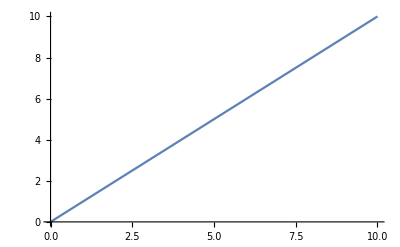

0.001

```mathematica
NDSolve[{3 R[r] R''[r]==2 R'[r]^2 (-1+R'[r]^2),R[0]==0.0000000000001,R'[0]==1},R[r],{r,0,10}]
R[r]/.%[[1]]
Plot[%/.r->rt,{rt,0,10}]
%%/.r->0.001
```

{{R[r]→InterpolatingFunction[…][r]}}

InterpolatingFunction[…][r]

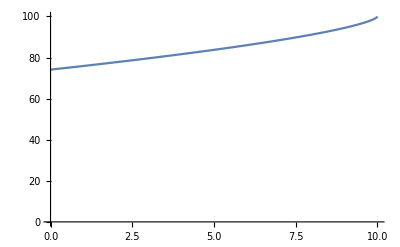

94.4654

```mathematica
NDSolve[{3 R[r] R''[r]==2 R'[r]^2 (-1+R'[r]^2),R[10]==100,R'[10]==200},R[r],{r,0,10}]
R[r]/.%[[1]]
Plot[%/.r->rt,{rt,0,10},PlotRange->{0,100}]
%%/.r->9
```

```mathematica
L =P[r]^3/P'[r] √(P'[r]^2-l^2/P[r]^2 2V[P[r]])
dLdPp=Simplify[D[L,P'[r]]]
dLdP = Simplify[D[L,P[r]]]
Rppsol = Simplify[Solve[Simplify[D[dLdPp,r]]==dLdP,P''[r]]][[1]]
```

(P[r]^3 √(-(2 l^2 V[P[r]])/P[r]^2+P'[r]^2))/P'[r]

(2 l^2 P[r] V[P[r]])/(P'[r]^2 √(-(2 l^2 V[P[r]])/P[r]^2+P'[r]^2))

(-4 l^2 V[P[r]]+P[r] (3 P[r] P'[r]^2-l^2 V'[P[r]]))/(P'[r] √(-(2 l^2 V[P[r]])/P[r]^2+P'[r]^2))

{P''[r]→(P'[r]^2 (16 l^4 V[P[r]]^2+3 P[r]^3 P'[r]^2 (P[r] P'[r]^2-l^2 V'[P[r]])+4 l^2 P[r] V[P[r]] (-3 P[r] P'[r]^2+l^2 V'[P[r]])))/(2 l^2 P[r] V[P[r]] (4 l^2 V[P[r]]-3 P[r]^2 P'[r]^2))}

```mathematica
L =P[r]^3 R[r]^2 √(1/(R'[r]^2-1)l^2/P[r]^4+1)
dLdRp=Simplify[D[L,R'[r]]]
dLdR = Simplify[D[L,R[r]]]
Simplify[D[dLdRp,r]]-dLdR
Rppsol = Simplify[Solve[Simplify[D[dLdRp,r]]==dLdR,R''[r]]][[1]]
```

P[r]^3 R[r]^2 √(1+l^2/(P[r]^4 (-1+R'[r]^2)))

-(l^2 R[r]^2 R'[r])/(P[r] (-1+R'[r]^2)^2 √(1+l^2/(P[r]^4 (-1+R'[r]^2))))

2 P[r]^3 R[r] √(1+l^2/(P[r]^4 (-1+R'[r]^2)))

-2 P[r]^3 R[r] √(1+l^2/(P[r]^4 (-1+R'[r]^2)))+(l^2 R[r] (-2 P[r] R'[r]^2 (-1+R'[r]^2) (l^2+P[r]^4 (-1+R'[r]^2))+R[r] (-P'[r] R'[r] (-1+R'[r]^2) (l^2-P[r]^4 (-1+R'[r]^2))+P[r] (l^2 (1+2 R'[r]^2)+P[r]^4 (-1-2 R'[r]^2+3 R'[r]^4)) R''[r])))/(P[r]^2 (-1+R'[r]^2)^3 √(1+l^2/(P[r]^4 (-1+R'[r]^2))) (l^2+P[r]^4 (-1+R'[r]^2)))

{R''[r]→((-1+R'[r]^2) (l^4 R[r] P'[r] R'[r]-l^2 P[r]^4 R[r] P'[r] R'[r] (-1+R'[r]^2)+2 P[r]^9 (-1+R'[r]^2)^3+2 l^4 P[r] (-1+2 R'[r]^2)+2 l^2 P[r]^5 (2-5 R'[r]^2+3 R'[r]^4)))/(l^2 P[r] R[r] (l^2 (1+2 R'[r]^2)+P[r]^4 (-1-2 R'[r]^2+3 R'[r]^4)))}

```mathematica
L =P[r,τ]^3/D[P[r,τ],r]^2 √(D[P[r,τ],r]^2+l^2/P[r,τ]^2 D[P[r,τ],τ]^2)
dLdPr=Simplify[D[L,D[P[r,τ],r]]]
dLdPτ=Simplify[D[L,D[P[r,τ],τ]]]
dLdP = Simplify[D[L,P[r,τ]]]
Simplify[(D[dLdPp,r]+D[dLdPτ,τ]-dLdP)√((l^2 (Derivative[0,1][P][r,τ])^2)/P[r,τ]^2+(Derivative[1,0][P][r,τ])^2) (l^2 (Derivative[0,1][P][r,τ])^2 Derivative[1,0][P][r,τ]+P[r,τ]^2 (Derivative[1,0][P][r,τ])^3)]
```

(P[r,τ]^3 √((l^2 (P^(0,1)[r,τ])^2)/P[r,τ]^2+(P^(1,0)[r,τ])^2))/((P^(1,0)[r,τ])^2)

-(P[r,τ] (2 l^2 (P^(0,1)[r,τ])^2+P[r,τ]^2 (P^(1,0)[r,τ])^2))/((P^(1,0)[r,τ])^3 √((l^2 (P^(0,1)[r,τ])^2)/P[r,τ]^2+(P^(1,0)[r,τ])^2))

(l^2 P[r,τ] P^(0,1)[r,τ])/((P^(1,0)[r,τ])^2 √((l^2 (P^(0,1)[r,τ])^2)/P[r,τ]^2+(P^(1,0)[r,τ])^2))

(2 l^2 (P^(0,1)[r,τ])^2+3 P[r,τ]^2 (P^(1,0)[r,τ])^2)/((P^(1,0)[r,τ])^2 √((l^2 (P^(0,1)[r,τ])^2)/P[r,τ]^2+(P^(1,0)[r,τ])^2))

-6 l^2 P[r,τ]^3 P^(0,1)[r,τ] P^(1,1)[r,τ]-(4 l^4 P[r,τ] (P^(0,1)[r,τ])^3 P^(1,1)[r,τ])/((P^(1,0)[r,τ])^2)+(2 l^4 (P^(0,1)[r,τ])^4 (-2 (P^(1,0)[r,τ])^2+3 P[r,τ] P^(2,0)[r,τ]))/((P^(1,0)[r,τ])^3)+(l^2 P[r,τ]^2 (P^(0,1)[r,τ])^2 (-10 (P^(1,0)[r,τ])^2+9 P[r,τ] P^(2,0)[r,τ]))/(P^(1,0)[r,τ])+P[r,τ]^3 P^(1,0)[r,τ] (l^2 P^(0,2)[r,τ]+2 P[r,τ] (-3 (P^(1,0)[r,τ])^2+P[r,τ] P^(2,0)[r,τ]))

```mathematica
L =P[r]^3 √(1-l^2/P[r]^2(2V[P[r]])/P'[r]^2)
dLdPp=Simplify[D[L,P'[r]]]
dLdP = Simplify[D[L,P[r]]]
Rppsol = Simplify[Solve[Simplify[D[dLdPp,r]]==dLdP,P''[r]]][[1]]
```

P[r]^3 √(1-(2 l^2 V[P[r]])/(P[r]^2 P'[r]^2))

(2 l^2 P[r] V[P[r]])/(√(1-(2 l^2 V[P[r]])/(P[r]^2 P'[r]^2)) P'[r]^3)

(-4 l^2 V[P[r]]+P[r] (3 P[r] P'[r]^2-l^2 V'[P[r]]))/(√(1-(2 l^2 V[P[r]])/(P[r]^2 P'[r]^2)) P'[r]^2)

{P''[r]→(P'[r]^2 (16 l^4 V[P[r]]^2+3 P[r]^3 P'[r]^2 (P[r] P'[r]^2-l^2 V'[P[r]])+4 l^2 P[r] V[P[r]] (-3 P[r] P'[r]^2+l^2 V'[P[r]])))/(2 l^2 P[r] V[P[r]] (4 l^2 V[P[r]]-3 P[r]^2 P'[r]^2))}

```mathematica
L =P[r]^3 R[r]^2 √(1/(R'[r]^2-1)l^2/P[r]^4+1)

dLdR = Simplify[D[L,P[r]]]
(*dLdRp=Simplify[D[L,R'[r]]]
dLdR = Simplify[D[L,R[r]]]
Simplify[D[dLdRp,r]]-dLdR
Rppsol = Simplify[Solve[Simplify[D[dLdRp,r]]==dLdR,R''[r]]][[1]]*)
```

P[r]^3 R[r]^2 √(1+l^2/(P[r]^4 (-1+R'[r]^2)))

(R[r]^2 (l^2+3 P[r]^4 (-1+R'[r]^2)))/(P[r]^2 (-1+R'[r]^2) √(1+l^2/(P[r]^4 (-1+R'[r]^2))))

#### Cosmo

```mathematica
Psol=P[τ]/.DSolve[D[P[τ],τ]==P[τ]H,P[τ],τ][[1]]/.C[1]->P0
```

ⅇ^(H τ) P0

(ⅇ^(3 H τ) P0^3)/(√(ⅇ^(2 H τ) P0^2+ⅇ^(2 H τ) H^2 P0^2))

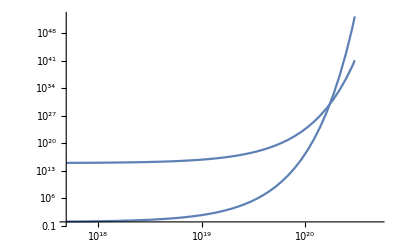

```mathematica
Pg=(g[p]Psol)/(√(g[p]+Psol^2 H^2))/.g[p]->Psol^2
Show[{LogLogPlot[Pg/.{P0->1,H->2 10^-19}/.τ->τt,{τt,0,5 10^20}],LogLogPlot[Pg/.{P0->30000000,H->1 10^-19}/.τ->τt,{τt,0,5 10^20}]}]
```

```mathematica
N[E^60]
```

1.14201×10^26

```mathematica
DSolve[D[P[τ],τ]==√(k - H^2 P[τ]^2),P[τ],τ]
```

{{P[τ]→-(√k Tan[H (τ+C[1])])/(H √(1+Tan[H (τ+C[1])]^2))},{P[τ]→(√k Tan[H (τ+C[1])])/(H √(1+Tan[H (τ+C[1])]^2))}}

```mathematica
Series[Tan[x]/(√(1+Tan[x]^2)),{x,0,1}]
```

x+O[x]^2

```mathematica
DSolve[D[P[τ],τ]== H P[τ],P[τ],τ]
```

{{P[τ]→ⅇ^(H τ) C[1]}}

```mathematica
DSolve[D[T[τ],τ]==l/(P0 E^(H τ)) √(1+l^2 H^2),T[τ],τ]
```

{{T[τ]→-(ⅇ^(-H τ) l √(1+H^2 l^2))/(H P0)+C[1]}}

## New basis - Rdot=0 with opposite sign u^t

#### Metric and connection

```mathematica
Needs["Greater2`"];
```

Christoffel::shdw: Symbol Christoffel appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

x::shdw: Symbol x appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

k::shdw: Symbol k appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

l::shdw: Symbol l appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

p::shdw: Symbol p appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

X::shdw: Symbol X appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

T::shdw: Symbol T appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

g::shdw: Symbol g appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

t::shdw: Symbol t appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents

Needs::nocont: Context Greater2` was not created when Needs was evaluated.

```mathematica
gp = {{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2 r^2,0,0},{0,0,0,p^2/l^2 r^2 Cos[θ]^2,0},{0,0,0,0,1/g[p]}}
X= {t,r,θ,ϕ,p};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gp//MatrixForm 
Simplify[Det[gp]]
Γp=Christoffel[gp, X];

(*/.{g[p]->g[p[τ]],g'[p]->g'[p[τ]]}*)
```

{{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,(p^2 r^2)/l^2,0,0},{0,0,0,(p^2 r^2 Cos[θ]^2)/l^2,0},{0,0,0,0,1/g[p]}}

(-g[p] | 0 | 0 | 0 | 0
0 | p^2/l^2 | 0 | 0 | 0
0 | 0 | (p^2 r^2)/l^2 | 0 | 0
0 | 0 | 0 | (p^2 r^2 Cos[θ]^2)/l^2 | 0
0 | 0 | 0 | 0 | 1/g[p])

-(p^6 r^4 Cos[θ]^2)/l^6

#### Find basis

```mathematica
u = {uT,0,0,0,D[P[r,τ],τ]}
nM = {nT,0,0,0,nP}
er = {erT,D[R[r],r],0,0,D[P[r,τ],r]}
uTsol=Solve[u.gp.u==-1,uT][[1]]
erTsol=erT/.Simplify[Solve[er.gp.nM==0,erT]][[1]]

nP/.Simplify[Solve[nM.gp.nM==1,nP]][[2]]
nP/.Solve[u.gp.nM==0,nP][[1]]
nTsol=Simplify[nT/.Solve[%==%%,nT][[2]]/.uTsol](*nT sol*)
nPsol=Simplify[%%/.nT->%/.uTsol]
Print["Rp sol is"]
Rpsol=Simplify[PowerExpand[R'[r]/.Simplify[Solve[er.gp.er==p^2/l^2,R'[r]]][[2]]/.erT->erTsol/.{nT->nTsol,nP->nPsol}]]

Print["\n"]

utest = {uT,0,0,0,D[P[r,τ],τ]}/.uTsol
ntest =PowerExpand[ {nT,0,0,0,nP}/.{nT->nTsol,nP->nPsol}]
ertest = PowerExpand[{erT,D[R[r],r],0,0,D[P[r,τ],r]}/.R'[r]->Rpsol/.erT->erTsol/.{nT->nTsol,nP->nPsol}]

Print["\n"]

Simplify[utest.gp.utest]
Simplify[ntest.gp.ntest]
Simplify[ertest.gp.ertest]
Simplify[utest.gp.ntest]
Simplify[utest.gp.ertest]
Simplify[ntest.gp.ertest]
```

{uT,0,0,0,P^(0,1)[r,τ]}

{nT,0,0,0,nP}

{erT,R'[r],0,0,P^(1,0)[r,τ]}

{uT→-(√(g[p]+(P^(0,1)[r,τ])^2))/g[p]}

(nP P^(1,0)[r,τ])/(nT g[p]^2)

√g[p] √(1+nT^2 g[p])

(nT uT g[p]^2)/(P^(0,1)[r,τ])

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(P^(0,1)[r,τ])/(√(g[p]^2))

-(√(g[p]^2) √(g[p]+(P^(0,1)[r,τ])^2))/g[p]

Rp sol is

(√(g[p] (p^2+(l^2 (P^(1,0)[r,τ])^2)/((P^(0,1)[r,τ])^2))))/(p √g[p])

{-(√(g[p]+(P^(0,1)[r,τ])^2))/g[p],0,0,0,P^(0,1)[r,τ]}

{(P^(0,1)[r,τ])/g[p],0,0,0,-√(g[p]+(P^(0,1)[r,τ])^2)}

{-(√(g[p]+(P^(0,1)[r,τ])^2) P^(1,0)[r,τ])/(g[p] P^(0,1)[r,τ]),(√(p^2+(l^2 (P^(1,0)[r,τ])^2)/((P^(0,1)[r,τ])^2)))/p,0,0,P^(1,0)[r,τ]}

-1

1

p^2/l^2

0

-(P^(1,0)[r,τ])/(P^(0,1)[r,τ])

0

```mathematica
gp
```

{{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,(p^2 r^2)/l^2,0,0},{0,0,0,(p^2 r^2 Cos[θ]^2)/l^2,0},{0,0,0,0,1/g[p]}}

### use analytic expression from notes

#### prefactor for t and r components

```mathematica
Simplify[(-utest[[1]] (ntest[[5]])/(ntest[[1]])+utest[[5]])]
```

-g[p]/(P^(0,1)[r,τ])

```mathematica
Simplify[(-ertest[[1]] (ntest[[5]])/(ntest[[1]])+ertest[[5]])]
```

-(g[p] P^(1,0)[r,τ])/((P^(0,1)[r,τ])^2)

#### angular connection

Check angular is consistent with the formula I derived

```mathematica
Table[Γp[[i,3;;4,5]](gp.ntest)[[i]],{i,5}]
Table[Γp[[i,3;;4,1]](gp.ntest)[[i]],{i,5}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0}}

{{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
(gp.ntest)
```

{-P^(0,1)[r,τ],0,0,0,-(√(g[p]+(P^(0,1)[r,τ])^2))/g[p]}

```mathematica
Table[Γp[[i,3;;4,3;;4]](gp.ntest)[[i]],{i,5}]/.nr->0
```

{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{(p r^2 √(g[p]+(P^(0,1)[r,τ])^2))/l^2,0},{0,(p r^2 Cos[θ]^2 √(g[p]+(P^(0,1)[r,τ])^2))/l^2}}}

#### non - angular gammas

```mathematica
Table[Γp[[i,;;,5]](gp.ntest/.nr->0)[[i]],{i,5}];
%//MatrixForm
(*%%/.nrepl//MatrixForm*)
```

(-(g'[p] P^(0,1)[r,τ])/(2 g[p]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (g'[p] √(g[p]+(P^(0,1)[r,τ])^2))/(2 g[p]^2))

```mathematica
-utest.Sum[Γp[[i,;;,5]](gp.ntest)[[i]],{i,5}]
(*/.nrepl*)
```

-1/g[p]^2 g'[p] P^(0,1)[r,τ] √(g[p]+(P^(0,1)[r,τ])^2)

```mathematica
-ertest.Sum[Γp[[i,;;,5]](gp.ntest)[[i]],{i,5}]
(*/.nrepl*)
```

-1/g[p]^2 g'[p] √(g[p]+(P^(0,1)[r,τ])^2) P^(1,0)[r,τ]

#### Cosmo

```mathematica
Psol=P[τ]/.DSolve[D[P[τ],τ]==P[τ]H,P[τ],τ][[1]]/.C[1]->P0
```

ⅇ^(H τ) P0

```mathematica
Pg=(g[p]Psol)/(√(g[p]+Psol^2 H^2))/.g[p]->Psol^2
Show[{LogLogPlot[Pg/.{P0->1,H->2 10^-19}/.τ->τt,{τt,0,5 10^20}],LogLogPlot[Pg/.{P0->30000000,H->1 10^-19}/.τ->τt,{τt,0,5 10^20}]}]
```

(ⅇ^(3 H τ) P0^3)/(√(ⅇ^(2 H τ) P0^2+ⅇ^(2 H τ) H^2 P0^2))

-Graphics-

```mathematica
N[E^60]
```

1.14201×10^26

```mathematica
DSolve[D[P[τ],τ]==√(k - H^2 P[τ]^2),P[τ],τ]
```

{{P[τ]→-(√k Tan[H (τ+C[1])])/(H √(1+Tan[H (τ+C[1])]^2))},{P[τ]→(√k Tan[H (τ+C[1])])/(H √(1+Tan[H (τ+C[1])]^2))}}

```mathematica
Series[Tan[x]/(√(1+Tan[x]^2)),{x,0,1}]
```

x+O[x]^2

```mathematica
DSolve[D[P[τ],τ]== H P[τ],P[τ],τ]
```

{{P[τ]→ⅇ^(H τ) C[1]}}

```mathematica
DSolve[D[T[τ],τ]==l/(P0 E^(H τ)) √(1+l^2 H^2),T[τ],τ]
```

{{T[τ]→-(ⅇ^(-H τ) l √(1+H^2 l^2))/(H P0)+C[1]}}

```mathematica
DSolve[D[χ[r],r]==1/(√(1-(r/l^2)^2)),]
```

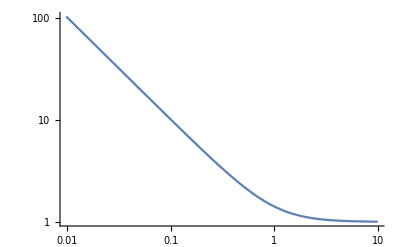

```mathematica
LogLogPlot[(√(1+x^2))/x,{x,0,10}]
```

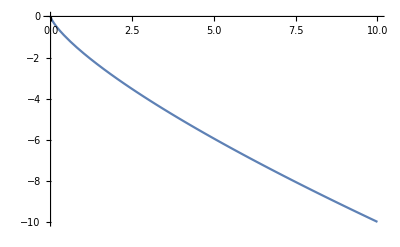

```mathematica
Plot[-ρ(1-(1- ω/ρ))^(3/4)/.ρ->10,{ω,0,10}]
```

#### Plot solutions to effective potential

{{P[τ]→-(√(2-ⅇ^(-2 √3 (τ+C[1]))+23 ⅇ^(2 √3 (τ+C[1]))))/(2 √3)},{P[τ]→(√(2-ⅇ^(-2 √3 (τ+C[1]))+23 ⅇ^(2 √3 (τ+C[1]))))/(2 √3)}}

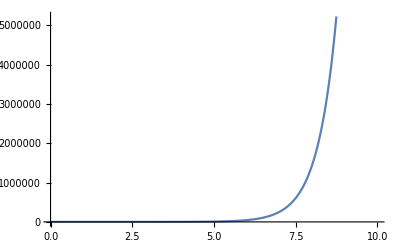

```mathematica
DSolve[D[P[τ],τ]==√(-1 + 1/P[τ]^2 2+P[τ]^2 3),P[τ],τ]
Plot[(P[τ]/.%[[2]])/.{C[1]->0}/.τ->τt,{τ,0,10}]
```

{{P[τ]→-(√(2-ⅇ^(-2 √H (τ+C[1]))-ⅇ^(2 √H (τ+C[1]))+4 ⅇ^(2 √H (τ+C[1])) H ρ))/(2 √H)},{P[τ]→(√(2-ⅇ^(-2 √H (τ+C[1]))-ⅇ^(2 √H (τ+C[1]))+4 ⅇ^(2 √H (τ+C[1])) H ρ))/(2 √H)}}

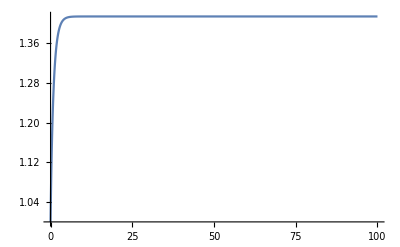

```mathematica
DSolve[D[P[τ],τ]==√(-1 + 1/P[τ]^2 ρ+P[τ]^2 H),P[τ],τ]
Plot[(P[τ]/.%[[2]])/.{C[1]->0}/.{ρ->1,H->0.25}/.τ->τt,{τ,0,100},PlotRange->All]
```

{{P[τ]→-(ⅇ^(-√H (τ+C[1])) √(ⅇ^(4 √H (τ+C[1])) √H-√H ρ))/(√2 √H)},{P[τ]→(ⅇ^(-√H (τ+C[1])) √(ⅇ^(4 √H (τ+C[1])) √H-√H ρ))/(√2 √H)}}

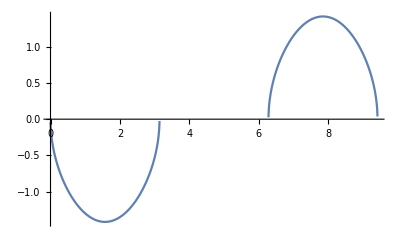

```mathematica
DSolve[D[P[τ],τ]==√(1/P[τ]^2 ρ+P[τ]^2 H),P[τ],τ]
Plot[(P[τ]/.%[[2]])/.{C[1]->0}/.{ρ->1,H->-0.25}/.τ->τt,{τ,0,10},PlotRange->All]
```

```mathematica
Solve[k + P^2/l^2-μ/P^2==0,P]
Solve[ P^2/l^2-μ/P^2==0,P]
```

{{P→-(√(-k l^2-√(l^2 (k^2 l^2+4 μ))))/(√2)},{P→(√(-k l^2-√(l^2 (k^2 l^2+4 μ))))/(√2)},{P→-(√(-k l^2+√(l^2 (k^2 l^2+4 μ))))/(√2)},{P→(√(-k l^2+√(l^2 (k^2 l^2+4 μ))))/(√2)}}

{{P→-√l μ^(1/4)},{P→-ⅈ √l μ^(1/4)},{P→ⅈ √l μ^(1/4)},{P→√l μ^(1/4)}}

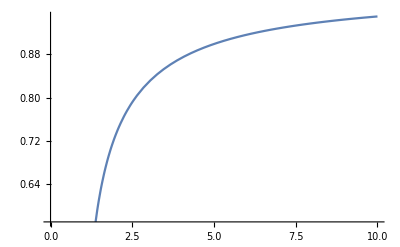

```mathematica
Plot[1 + √(-1+x^2) - x,{x,0,10}]
```

```mathematica
Normal[Series[l^2/2(-k + √(k+4 μ/l^2))/.k->1/.μ->ϵ l^2,{ϵ,0,1}]]/.ϵ->μ/l^2
Normal[Series[l^2/2(-k + √(k+4 μ/l^2))/.k->-1/.μ->ϵ l^2,{ϵ,∞,0}]]/.ϵ->μ/l^2
```

μ

l^2/2+l^2 √(μ/l^2)

#### get trace of K

```mathematica
ginddndn = {{-1,-Pp/Pd,0,0},
		{-Pp/Pd,P^2/l^2,0,0},
		{0,0,gθθ,0},
		{0,0,0,gϕϕ}}
```

{{-1,-Pp/Pd,0,0},{-Pp/Pd,P^2/l^2,0,0},{0,0,gθθ,0},{0,0,0,gϕϕ}}

```mathematica
Simplify[Inverse[ginddndn]]
```

{{-(P^2 Pd^2)/(P^2 Pd^2+l^2 Pp^2),-(l^2 Pd Pp)/(P^2 Pd^2+l^2 Pp^2),0,0},{-(l^2 Pd Pp)/(P^2 Pd^2+l^2 Pp^2),(l^2 Pd^2)/(P^2 Pd^2+l^2 Pp^2),0,0},{0,0,1/gθθ,0},{0,0,0,1/gϕϕ}}

```mathematica
ginddndn = {{-1,0,0,0},
		{0,P^2/l^2,0,0},
		{0,0,gθθ,0},
		{0,0,0,gϕϕ}}
Kdndn= {{-1 npd/Pd,0,0,0},
		{0,np/P P^2/l^2,0,0},
		{0,0,np/P gθθ,0},
		{0,0,0,np/P gϕϕ}}
```

{{-1,0,0,0},{0,P^2/l^2,0,0},{0,0,gθθ,0},{0,0,0,gϕϕ}}

{{-npd/Pd,0,0,0},{0,(np P)/l^2,0,0},{0,0,(gθθ np)/P,0},{0,0,0,(gϕϕ np)/P}}

```mathematica
Kdndn.Inverse[ginddndn]
```

{{npd/Pd,0,0,0},{0,np/P,0,0},{0,0,np/P,0},{0,0,0,np/P}}

```mathematica
Tr[Kdndn.Inverse[ginddndn]]
```

(3 np)/P+npd/Pd

```mathematica
Inverse[ginddndn].{ut,0,0,0}
```

{-ut,0,0,0}

#### parallel transporting along u

```mathematica
X = {Xt[τ],0,0,0,Xp[τ]}

Simplify[PowerExpand[Simplify[Simplify[Table[D[X,τ][[i]] + utest.Γp[[i,;;,;;]].X,{i,5}]]/.Derivative[0,1][P][r,τ]->p Hp/.g[p]->p^2/l^2/.g'[p]->2 p/l^2]]]
M5 = {{Hp,0,0,0,-l^2/p^2 √(Hp^2+1/l^2)},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
		{-√(Hp^2+1/l^2)p^2/l^2,0,0,0,-Hp}};
M5.X + D[X,τ]
```

{Xt[τ],0,0,0,Xp[τ]}

{-(√(Hp^2+1/l^2) l^2 Xp[τ])/p^2+Hp Xt[τ]+Xt'[τ],0,0,0,-Hp Xp[τ]-(√(Hp^2+1/l^2) p^2 Xt[τ])/l^2+Xp'[τ]}

{-(√(Hp^2+1/l^2) l^2 Xp[τ])/p^2+Hp Xt[τ]+Xt'[τ],0,0,0,-Hp Xp[τ]-(√(Hp^2+1/l^2) p^2 Xt[τ])/l^2+Xp'[τ]}

```mathematica
X2= {Xt[τ],Xp[τ]}/.{Xt[τ]->A E^(n Hp τ),Xp[τ]->E^(m Hp τ)};
M = {{Hp,-l^2/p^2 √(Hp^2+1/l^2)},
		{-√(Hp^2+1/l^2)p^2/l^2,-Hp}};

(*Simplify[(Simplify[Inverse[M]].M)]
Simplify[Inverse[M].D[X2,τ] + D[X2]]*)
eqn=Simplify[(M.X2/.p->p0 E^(Hp τ))+D[X2,τ]]
Asol1 = Solve[eqn[[1]]==0,A][[1]]
Simplify[(eqn[[2]]/.%[[1]])]
msol1 = Simplify[Solve[%==0,m]][[1]]
nrepl =Simplify[Solve[(D[A/.Asol1,τ]/.msol1)==0,n][[1]]]
msol = msol1/.nrepl
Asol=PowerExpand[Simplify[Asol1/.msol/.nrepl]]
(*Asol=A->-l^2/p0^2*)
X2sol =PowerExpand[Simplify[X2/.Asol/.msol[[1]]/.nrepl]]
Simplify[((M.X2sol/.p->p0 E^(Hp τ)) + D[X2sol,τ])]
```

{A ⅇ^(Hp n τ) Hp (1+n)-(ⅇ^(Hp (-2+m) τ) √(Hp^2+1/l^2) l^2)/p0^2,ⅇ^(Hp m τ) Hp (-1+m)-(A ⅇ^(Hp (2+n) τ) √(Hp^2+1/l^2) p0^2)/l^2}

{A→(ⅇ^(Hp (-2+m) τ-Hp n τ) √(Hp^2+1/l^2) l^2)/(Hp (1+n) p0^2)}

(ⅇ^(Hp m τ) (-1+Hp^2 l^2 (-2+m-n+m n)))/(Hp l^2 (1+n))

{m→(2+1/(Hp^2 l^2)+n)/(1+n)}

{n→-1-(√(l^2+Hp^2 l^4))/(Hp l^2)}

{m→-(Hp l^2 (1+1/(Hp^2 l^2)-(√(l^2+Hp^2 l^4))/(Hp l^2)))/(√(l^2+Hp^2 l^4))}

{A→-(√(Hp^2+1/l^2) l^4)/(√(l^2+Hp^2 l^4) p0^2)}

{-(ⅇ^(-((Hp l^2+√(l^2+Hp^2 l^4)) τ)/l^2) √(Hp^2+1/l^2) l^4)/(√(l^2+Hp^2 l^4) p0^2),ⅇ^(((-1-Hp^2 l^2+Hp √(l^2+Hp^2 l^4)) τ)/(√(l^2+Hp^2 l^4)))}

{0,0}

```mathematica
Simplify[X2sol]
```

{-(ⅇ^(-((Hp l^2+√(l^2+Hp^2 l^4)) τ)/l^2) √(Hp^2+1/l^2) l^4)/(√(l^2+Hp^2 l^4) p0^2),ⅇ^(((-1-Hp^2 l^2+Hp √(l^2+Hp^2 l^4)) τ)/(√(l^2+Hp^2 l^4)))}

```mathematica
Solve[(D[A/.Asol1,τ]/.msol1)==0,n]
```

{{n→(-l^2-(√(l^2+Hp^2 l^4))/Hp)/l^2},{n→(-l^2+(√(l^2+Hp^2 l^4))/Hp)/l^2}}

```mathematica
Simplify[X2sol[[1]]^2 gp[[1,1]]+X2sol[[2]]^2 gp[[5,5]]/.Derivative[0,1][P][r,τ]->p Hp/.g[p]->p^2/l^2/.g'[p]->2 p/l^2/.p->p0 E^(Hp τ)]
```

0

so it’s a lightlike vector that is parrallel transported

#### parallel transporting along lightlike trajectory

```mathematica
null = {xtn,0,0,0,xpn};
null=Simplify[null/.Solve[null.gp.null==0,xtn][[2]]]
```

{xpn/g[p],0,0,0,xpn}

```mathematica
X = {Xt[τ],0,0,0,Xp[τ]}

Simplify[PowerExpand[Simplify[Simplify[Table[D[X,τ][[i]] + null.Γp[[i,;;,;;]].X,{i,5}]]/.Derivative[0,1][P][r,τ]->p Hp/.g[p]->p^2/l^2/.g'[p]->2 p/l^2]]]
M5 =xpn {{1/p,0,0,0,l^2/p^3},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
		{p/l^2,0,0,0,-1/p}};
M5.X + D[X,τ]
```

{Xt[τ],0,0,0,Xp[τ]}

{(l^2 xpn Xp[τ])/p^3+(xpn Xt[τ])/p+Xt'[τ],0,0,0,-(xpn Xp[τ])/p+(p xpn Xt[τ])/l^2+Xp'[τ]}

{(l^2 xpn Xp[τ])/p^3+(xpn Xt[τ])/p+Xt'[τ],0,0,0,-(xpn Xp[τ])/p+(p xpn Xt[τ])/l^2+Xp'[τ]}

```mathematica
X2= {Xt[τ],Xp[τ]}/.{Xt[τ]->A E^(n Hp τ),Xp[τ]->E^(m Hp τ)};
M =xpn {{1/p,l^2/p^3},
	{p/l^2,-1/p}}/.xpn->p0/l E^(Hp τ)(*/.xpn-> E^(Hp τ)*)

(*Simplify[(Simplify[Inverse[M]].M)]
Simplify[Inverse[M].D[X2,τ] + D[X2]]*)
eqn=Simplify[(M.X2/.p->p0 E^(Hp τ))+D[X2,τ]]
Asol1 = Solve[eqn[[1]]==0,A][[1]]
Simplify[(eqn[[2]]/.%[[1]])];
msol1 = Simplify[Solve[%==0,m]][[1]]
nrepl =Simplify[Solve[(D[A/.Asol1,τ]/.msol1)==0,n][[1]]]
msol = msol1/.nrepl
Asol=PowerExpand[Simplify[Asol1/.msol/.nrepl]]
(*Asol=A->-l^2/p0^2*)
X2sol =FullSimplify[PowerExpand[Simplify[X2/.Asol/.msol[[1]]/.nrepl]]]
FullSimplify[((M.X2sol/.p-> p0 E^(Hp τ)) + D[X2sol,τ])]
```

{{(ⅇ^(Hp τ) p0)/(l p),(ⅇ^(Hp τ) l p0)/p^3},{(ⅇ^(Hp τ) p p0)/l^3,-(ⅇ^(Hp τ) p0)/(l p)}}

{(A ⅇ^(Hp n τ) (1+Hp l n))/l+(ⅇ^(Hp (-2+m) τ) l)/p0^2,(ⅇ^(Hp m τ) l^2 (-1+Hp l m)+A ⅇ^(Hp (2+n) τ) p0^2)/l^3}

{A→-(ⅇ^(Hp (-2+m) τ-Hp n τ) l^2)/((1+Hp l n) p0^2)}

{m→(2+Hp l n)/(Hp l+Hp^2 l^2 n)}

{n→-1-(√(Hp^2 l^2 (2-2 Hp l+Hp^2 l^2)))/(Hp^2 l^2)}

{m→(2+Hp l (-1-(√(Hp^2 l^2 (2-2 Hp l+Hp^2 l^2)))/(Hp^2 l^2)))/(Hp l+Hp^2 l^2 (-1-(√(Hp^2 l^2 (2-2 Hp l+Hp^2 l^2)))/(Hp^2 l^2)))}

{A→(Hp l^3)/((-Hp l+Hp^2 l^2+Hp l √(2-2 Hp l+Hp^2 l^2)) p0^2)}

{(ⅇ^(-((Hp l+√(2+Hp l (-2+Hp l))) τ)/l) l^2)/((-1+Hp l+√(2+Hp l (-2+Hp l))) p0^2),ⅇ^((Hp l τ-√(2+Hp l (-2+Hp l)) τ)/l)}

{0,0}

```mathematica
FullSimplify[X2sol[[1]]^2 gp[[1,1]]+X2sol[[2]]^2 gp[[5,5]]/.Derivative[0,1][P][r,τ]->p Hp/.g[p]->p^2/l^2/.g'[p]->2 p/l^2/.p->p0 E^(Hp τ)]
```

(2 ⅇ^(-(2 √(2+Hp l (-2+Hp l)) τ)/l) l^2 (-1+Hp l))/((-1+Hp l+√(2+Hp l (-2+Hp l))) p0^2)

so it’s a spacelike vector that is parrallel transported

```mathematica
X2= {Xt[τ],Xp[τ]}/.{Xt[τ]->E^(n Hp τ),Xp[τ]->A E^(m Hp τ)};
M =xpn {{1/p,l^2/p^3},
	{p/l^2,-1/p}}/.xpn->p0/l E^(Hp τ)(*/.xpn-> E^(Hp τ)*)

(*Simplify[(Simplify[Inverse[M]].M)]
Simplify[Inverse[M].D[X2,τ] + D[X2]]*)
eqn=Simplify[(M.X2/.p->p0 E^(Hp τ))+D[X2,τ]]
Asol1 = Solve[eqn[[1]]==0,A][[1]]
Simplify[(eqn[[2]]/.%[[1]])];
msol1 = Simplify[Solve[%==0,m]][[1]]
nrepl =Simplify[Solve[(D[A/.Asol1,τ]/.msol1)==0,n][[1]]]
msol = msol1/.nrepl
Asol=PowerExpand[Simplify[Asol1/.msol/.nrepl]]
(*Asol=A->-l^2/p0^2*)
X2sol =FullSimplify[PowerExpand[Simplify[X2/.Asol/.msol[[1]]/.nrepl]]]
FullSimplify[((M.X2sol/.p-> p0 E^(Hp τ)) + D[X2sol,τ])]
```

{{(ⅇ^(Hp τ) p0)/(l p),(ⅇ^(Hp τ) l p0)/p^3},{(ⅇ^(Hp τ) p p0)/l^3,-(ⅇ^(Hp τ) p0)/(l p)}}

{ⅇ^(Hp n τ) (1/l+Hp n)+(A ⅇ^(Hp (-2+m) τ) l)/p0^2,(A ⅇ^(Hp m τ) l^2 (-1+Hp l m)+ⅇ^(Hp (2+n) τ) p0^2)/l^3}

{A→-(ⅇ^(-Hp (-2+m) τ+Hp n τ) (1+Hp l n) p0^2)/l^2}

{m→(2+Hp l n)/(Hp l+Hp^2 l^2 n)}

{n→-1-(√(Hp^2 (2-2 Hp l+Hp^2 l^2)))/(Hp^2 l)}

{m→(2+Hp l (-1-(√(Hp^2 (2-2 Hp l+Hp^2 l^2)))/(Hp^2 l)))/(Hp l+Hp^2 l^2 (-1-(√(Hp^2 (2-2 Hp l+Hp^2 l^2)))/(Hp^2 l)))}

{A→((-Hp+Hp^2 l+Hp √(2-2 Hp l+Hp^2 l^2)) p0^2)/(Hp l^2)}

{ⅇ^(-((Hp l+√(2+Hp l (-2+Hp l))) τ)/l),(ⅇ^(((Hp l-√(2+Hp l (-2+Hp l))) τ)/l) (-1+Hp l+√(2+Hp l (-2+Hp l))) p0^2)/l^2}

{0,0}

```mathematica
Solve[(-1+Hp l+√(2+Hp l (-2+Hp l))/.Hp->ϵ/l)==0,Hp]
```

{}

```mathematica
N[(-1+Hp l+√(2+Hp l (-2+Hp l))/.Hp->ϵ/l)/.ϵ->-20]
```

0.023796

```mathematica
Integrate[Log[x],x]
Limit[%,x->0]
```

-x+x Log[x]

0

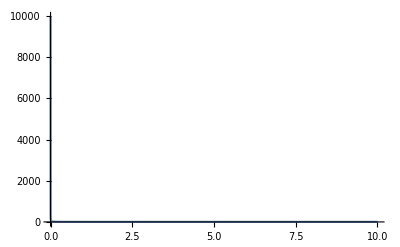

```mathematica
Plot[(√(1+x^2))/x,{x,0.0001,10},PlotRange->Full]
```

```mathematica
ph=Simplify[(p/.Simplify[Solve[1 - μ/p^2+p^2/l^2==0,p]][[4]])^2]^(1/2)
Simplify[(ph^3/.μ->ρM/A)-(ph^3/.μ->(ρM - ρω)/A)]
Simplify[Series[%,{ρω,0,1}]]
```

(√(-l^2+√(l^4+4 l^2 μ)))/(√2)

1/(2 √2)((-l^2+√(l^4+(4 l^2 ρM)/A))^(3/2)-(-l^2+√((l^2 (A l^2+4 ρM-4 ρω))/A))^(3/2))

(3 √(l^4+(4 l^2 ρM)/A) √(-l^2+√(l^4+(4 l^2 ρM)/A)) ρω)/(2 √2 (A l^2+4 ρM))+O[ρω]^2

```mathematica
Simplify[D[-(ph^3/.μ->(ρM - ρω)/A),ρω]/.ρω->0]
```

(3 l^2 √(-l^2+√(l^4+(4 l^2 ρM)/A)))/(2 √2 A √(l^4+(4 l^2 ρM)/A))

```mathematica
Simplify[D[-(ph/.μ->(ρM - ρω)/A),ρω]/.ρω->0]
```

l^2/(√2 A √(l^4+(4 l^2 ρM)/A) √(-l^2+√(l^4+(4 l^2 ρM)/A)))

```mathematica
Simplify[(ph^3/.μ->ρM/A)-(ph^3/.μ->(ρM - ρω)/A)]
Simplify[Series[%,{ρω,0,1}]]
```

1/(2 √2)((-l^2+√(l^4+(4 l^2 ρM)/A))^(3/2)-(-l^2+√((l^2 (A l^2+4 ρM-4 ρω))/A))^(3/2))

(3 √(l^4+(4 l^2 ρM)/A) √(-l^2+√(l^4+(4 l^2 ρM)/A)) ρω)/(2 √2 (A l^2+4 ρM))+O[ρω]^2

```mathematica
Simplify[DSolve[D[P[τ],τ]==√(P[τ]^2+a/P[τ]^4),P[τ],τ][[2]]]
```

{P[τ]→(ⅇ^(-τ-C[1]) (-a+ⅇ^(6 (τ+C[1])))^(1/3))/2^(1/3)}

```mathematica
DSolve[D[P[τ],τ]==√(P[τ]^2+a/P[τ]^3),P[τ],τ][[2]]
```

{P[τ]→(ⅇ^(-τ-C[1]) (-a+ⅇ^(5 τ+5 C[1]))^(2/5))/2^(2/5)}

```mathematica
DSolve[D[P[τ],τ]==√(b P[τ]^2+a/P[τ]^3),P[τ],τ][[2]]
```

{P[τ]→-((-1)^(1/5) ⅇ^(-√b (τ+C[1])) (-a+ⅇ^(5 √b (τ+C[1])))^(2/5))/(2^(2/5) b^(1/5))}

```mathematica
DSolve[D[P[τ],τ]==√(b P[τ]^2+a/P[τ]^m),P[τ],τ][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{P[τ]→(1/(√b)√a Sinh[1/2 (2 √b τ+√b m τ+2 √b C[1]+√b m C[1])])^(2/(2+m))}

```mathematica
DSolve[D[P[τ],τ]==√(a/P[τ]^m-1),P[τ],τ][[1]]
```

{P[τ]→InverseFunction[(Hypergeometric2F1[1/2,-1/m,1-1/m,a #1^-m] #1 √(1-a #1^-m))/(√(-1+a #1^-m))&][τ+C[1]]}

```mathematica
Simplify[DSolve[D[P[τ],τ]==a(P[τ]/l)^(-(1+3 ω)),P[τ],τ]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{P[τ]→(l^(3 ω) (2+3 ω) (a l τ+C[1]))^(1/(2+3 ω))}}

```mathematica
Simplify[DSolve[D[P[τ],τ]==(P[τ]/l)^(-(1+3 ω)),P[τ],τ]]/.ω->0
Simplify[DSolve[D[P[τ],τ]==a(P[τ]/l)^(-(1+3 ω)),P[τ],τ]]/.ω->1/3
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{P[τ]→√2 √(l τ+C[1])}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{P[τ]→3^(1/3) (l (a l τ+C[1]))^(1/3)}}

```mathematica
Series[√((ϵ+1)^2-1),{ϵ,0,1}]
```

√2 √ϵ+O[ϵ]^(3/2)

#### Solve for P in domination era

```mathematica
Pgen=P[τ]/.Simplify[DSolve[D[P[τ],τ]^2==2(P[τ]^2 ρ0)/(l^2 σc)(P[τ]/l)^(-3(1+ ω)),P[τ],τ]][[1]]
(*Matter Domination*)
MDP=Simplify[Pgen/.ω->0]
(C[1]/.Solve[MDP==P0[τ,η] ,C[1]][[1]])
MDP0ODE =P0[τ,η]/.Solve[D[%,τ]==0,P0[τ,η]][[1]];
DSolve[MDP0ODE==P0[τ,η],P0[τ,η],τ]

(*Radiation Domination*)
Simplify[Pgen/.ω->1/3]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(9/4)^(1/(3+3 ω)) ((l^(3 ω/2) (1+ω) (√2 √l √ρ0 τ+√σc C[1]))/(√σc))^(2/(3 (1+ω)))

(3/2)^(2/3) ((√2 √l √ρ0 τ)/(√σc)+C[1])^(2/3)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(-3 √2 √l √ρ0 τ+2 √σc P0[τ,η]^(3/2))/(3 √σc)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{P0[τ,η]→(3/2)^(2/3) ((-√2 √l √ρ0 τ+√σc C[1])/(√σc))^(2/3)},{P0[τ,η]→(3/2)^(2/3) ((√2 √l √ρ0 τ+√σc C[1])/(√σc))^(2/3)}}

√2 √((√2 l √ρ0 τ)/(√σc)+√l C[1])

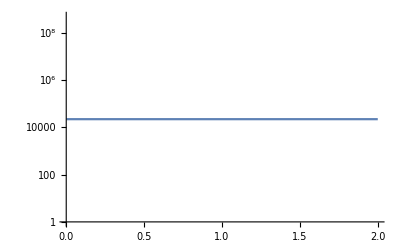

```mathematica
LogPlot[(E^Δη(HeavisideTheta[1-P] ( E^P)  + HeavisideTheta[P-1]HeavisideTheta[2-P](P)))/(HeavisideTheta[1-P] E^P  + HeavisideTheta[P-1]HeavisideTheta[2-P](P))/.P0->0.000001/.Δη->10,{P,0,2}]
```

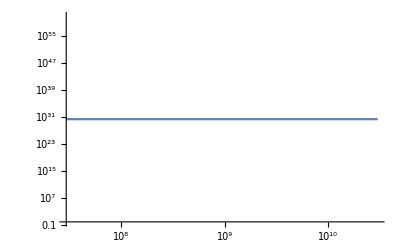

```mathematica
LogLogPlot[E^Δη((HeavisideTheta[x 1-P] ( E^P)  + HeavisideTheta[P-1 x]HeavisideTheta[x 2-P](P)^(1/2)+HeavisideTheta[P-x 2]HeavisideTheta[x 3-P](P)^(2/3)))/((HeavisideTheta[x 1-P] ( E^P)  + HeavisideTheta[P-x 1]HeavisideTheta[2x -P](P)^(1/2)+HeavisideTheta[P-x 2]HeavisideTheta[x 3-P](P)^(2/3)))/.x->10^10/.P0->10^2/.P1->10^1/.Δη->70,{P,0,3 10^10}]
```

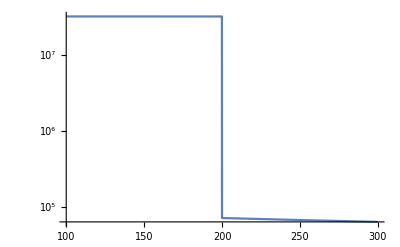

```mathematica
LogPlot[(( HeavisideTheta[P-1 x]HeavisideTheta[x 2-P](P0+P)^(1/2)+HeavisideTheta[P-x 2]HeavisideTheta[x 3-P]((P0+x 2)^(1/2)+P)^(2/3)))/(( HeavisideTheta[P-x 1]HeavisideTheta[2x -P](P1+P)^(1/2)+HeavisideTheta[P-x 2]HeavisideTheta[x 3-P]((P1+x 2)^(1/2)+P)^(2/3)))/.x->10^2/.P0->10^20/.P1->10^5/.Δη->10,{P,1 10^2,3 10^2}]
```

```mathematica
LogPlot[(( HeavisideTheta[P-1 x]HeavisideTheta[x 2-P](P0+P)^(1/2)+HeavisideTheta[P-x 2]HeavisideTheta[x 3-P]((P0+x 2)^(1/2)+P)^(2/3)))/(( HeavisideTheta[P-x 1]HeavisideTheta[2x -P](P1+P)^(1/2)+HeavisideTheta[P-x 2]HeavisideTheta[x 3-P]((P1+x 2)^(1/2)+P)^(2/3)))/.x->10^2/.P0->10^20/.P1->10^5/.Δη->10,{P,1 10^2,3 10^2}]
```

-Graphics-

```mathematica
LogLogPlot[((HeavisideTheta[x 1-P] ( E^P)  + HeavisideTheta[P-1 x]HeavisideTheta[x 2-P](P)^(1/2)+HeavisideTheta[P-x 2]HeavisideTheta[x 3-P](P)^(2/3)))/((HeavisideTheta[x 1-P] (E^P)  + HeavisideTheta[P-x 1]HeavisideTheta[2x -P](P1+E^x+P)^(1/2)+HeavisideTheta[P-x 2]HeavisideTheta[x 3-P](P)^(2/3)))/.x->10^10/.P0->10^2/.P1->10^1/.Δη->10,{P,0,3 10^10}]
```

```mathematica
LogPlot[(( HeavisideTheta[P-1 x]HeavisideTheta[x 2-P](P)^(1/2)+HeavisideTheta[P-x 2]HeavisideTheta[x 3-P]((P0+x 2)^(1/2)+P)^(2/3)))/(( HeavisideTheta[P-x 1]HeavisideTheta[2x -P](P)^(1/2)+HeavisideTheta[P-x 2]HeavisideTheta[x 3-P]((x 2)^(1/2)+P)^(2/3)))/.x->10^2/.P0->10^20/.P1->10^5/.Δη->10,{P,1 10^2,3 10^2}]
```

```mathematica
Integrate[η^(2/3),η]
```

(3 η^(5/3))/5

```mathematica
PowerExpand[Simplify[Series[(a τ + P^(3/2))^(2/3),{τ,0,1}]]]
```

P+(2 a τ)/(3 √P)+O[τ]^2

```mathematica
DSolve[D[P[η],η]==√(P[η]^2/l^2+a/P[η]^m),P[η],η][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{P[η]→(√a l Sinh[((2+m) (η+C[1]))/(2 l)])^(2/(2+m))}

```mathematica
Simplify[DSolve[D[P[η],η]==√(P[η]^2/l^2+a/P[η]),P[η],η][[1]]]
```

{P[η]→(-1/2)^(2/3) ⅇ^(-(η+C[1])/l) (ⅇ^((3 (η+C[1]))/l)-a l^2)^(2/3)}

```mathematica
Simplify[DSolve[D[P[η],η]==√(P[η]^2/l^2+a/P[η]^2),P[η],η][[1]]]
```

{P[η]→-(ⅇ^(-(η+C[1])/l) √(ⅇ^((4 (η+C[1]))/l)-a l^2))/(√2)}

```mathematica
(P[τ]^2 ρ0)/(l^2 σc)(P[τ]/l)^(-3(1+ ω))
```

```mathematica
DSolve[D[P[τ],τ]==√(P[τ]^2/l^2+(ρ0 l^(1+3 ω))/(σc  P[τ]^(1+3 ω))),P[τ],τ][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{P[τ]→(-(l^(3+3 ω) ρ0)/σc)^(1/(3+3 ω))}

```mathematica
Simplify[DSolve[D[P[η],η]==P[η]/l+a/P[η]^1,P[η],η][[1]]]
Simplify[DSolve[D[P[η],η]==P[η]/l+a/P[η]^2,P[η],η][[1]]]
Simplify[DSolve[D[P[η],η]==P[η]/l+a/P[η]^3,P[η],η][[1]]]
```

{P[η]→-√(ⅇ^(2 (η/l+C[1]))-a l)}

{P[η]→(ⅇ^(3 (η/l+C[1]))-a l)^(1/3)}

{P[η]→-(ⅇ^(4 (η/l+C[1]))-a l)^(1/4)}

```mathematica
Simplify[DSolve[D[P[η],η]==P[η]/l(1 +(ρ0 l^(3(1+ ω)))/(σc  P[η]^(3(1+ ω)))),P[η],η][[1]]]
%/.ω->0
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{P[η]→((ⅇ^((3 (1+ω) (η+l σc C[1]))/l)-l^(3+3 ω) ρ0)/σc)^(1/(3+3 ω))}

{P[η]→((ⅇ^((3 (η+l σc C[1]))/l)-l^3 ρ0)/σc)^(1/3)}

```mathematica
Pgen=P[τ]/.Simplify[DSolve[D[P[τ],τ]^2==2(P[τ]^2 ρ0)/(l^2 σc)(P[τ]/l)^(-3(1+ ω)),P[τ],τ]][[1]]
%/.ω->0
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(9/4)^(1/(3+3 ω)) ((l^(3 ω/2) (1+ω) (√2 √l √ρ0 τ+√σc C[1]))/(√σc))^(2/(3 (1+ω)))

(3/2)^(2/3) ((√2 √l √ρ0 τ+√σc C[1])/(√σc))^(2/3)

```mathematica
DSolve[D[P[τc],τc]==P[τc]^2 Hτ,P[τc],τc]
DSolve[D[P[τc],τc]==3 Hτ P[τc]^(1/2),P[τc],τc]
DSolve[D[P[τc],τc]==3 Hτ P[τc]^(-5/4),P[τc],τc]
```

{{P[τc]→1/(-Hτ τc-C[1])}}

{{P[τc]→1/4 (9 Hτ^2 τc^2+6 Hτ τc C[1]+C[1]^2)}}

{{P[τc]→(3/2)^(8/9) (3 Hτ τc+C[1])^(4/9)}}

```mathematica
Simplify[Solve[E^((η-ηir)H)==((τ l^(1/2) a + r P0^(3/2))^(2/3))/((τ l^(1/2) a + P0^(3/2))^(2/3)),r]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{r→(-a √l τ+(ⅇ^(H (η-ηir)) (P0^(3/2)+a √l τ)^(2/3))^(3/2))/P0^(3/2)}}

```mathematica
DSolve[D[P[τ],τ]==P[τ]/l √((ρ0 l^6)/(σc  P[τ]^6)-1),P[τ],τ]
```

{{P[τ]→InverseFunction[(Log[√σc #1^3+√(-l^6 ρ0+σc #1^6)] √(-l^6 ρ0+σc #1^6))/(3 √σc √(-1+(l^6 ρ0)/(σc #1^6)) #1^3)&][τ/l+C[1]]}}

```mathematica
D[P[τ],τ]==P[τ]/l
```